```mathematica
Needs["Utilities`"]
Needs["Dielectrics`"]
Needs["Constants`"]
Needs["OpticalFits`"]
Needs["EnergyLoss`"]
```

#### Load Fit Parameters

```mathematica
FeTotalparams =ReadIt[NotebookDirectory[]<>"../extract optical data/FeTotalparams"];
(*FeTotalparamsExtrapolatedν =ReadIt[NotebookDirectory[]<>"../extract optical data/FeTotalparamsExtrapolatedν"];
FeTotalparamsExtrapolatedνn =ReadIt[NotebookDirectory[]<>"../extract optical data/FeTotalparamsExtrapolatedνn"];*)
SiO2Totalparams= ReadIt[NotebookDirectory[]<>"../extract optical data/SiO2Totalparams"];
MgOTotalparams =ReadIt[NotebookDirectory[]<>"../extract optical data/MgOTotalparams"];
```

### with wider mass range and temperature enhancement

Also changed velocity bounds so they are above escape velocity while we compute κ_min

```mathematica
vescape
{2 10^-4,2 10^-1} "c" /.SIConstRepl
```

11200

{60000,60000000}

#### Run Iron

```mathematica
FeTotalparamscoreT={{},{},{},{},{},{}};
Do[FeTotalparamscoreT[[i]]=Utilities`ReplaceParams[FeTotalparams[[i]],βcore,"β"],{i,Length[FeTotalparams]}];
```

```mathematica
FeELOutputDictSIEnhancedTest= EnergyLossTableAndInterFITTotalParamsEnhanced[{2.5 10^3,2.5 10^12} ("JpereV")/("c")^2/.SIConstRepl,{2 10^-4,2 10^-1} "c" /.SIConstRepl,<|"mχ"->8,"vχ"->4|>,FeTotalparamscoreT,True,"FeELOutputDictSIEnhancedTest"]
```

1 of 32

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1987.19}. NIntegrate obtained 0.000334844 and 3.4852×10^-6 for the integral and error estimates.

For mχ = 4.45×10^-33 , vχ = 60000
L:	0.000334844 
Prefactor:	1.28051×10^14
dEdr:	4.28772×10^10

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {3559.6}. NIntegrate obtained 0.000269583 and 0.0000153292 for the integral and error estimates.

For mχ = 4.45×10^-33 , vχ = 60000
L:	0.000269583 
Prefactor:	9.67268×10^13
dEdr:	2.60759×10^10

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {7257.97}. NIntegrate obtained 0.000177397 and 0.000012255 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

For mχ = 4.45×10^-33 , vχ = 60000
L:	0.000177397 
Prefactor:	1.59371×10^15
dEdr:	2.8272×10^11

For mχ = 4.45×10^-33 , vχ = 60000
L:	0.0000490278 
Prefactor:	1.37274×10^16
dEdr:	6.73024×10^11

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

For mχ = 4.45×10^-33 , vχ = 60000
L:	3.02195×10^-6 
Prefactor:	7.48944×10^16
dEdr:	2.26327×10^11

For mχ = 4.45×10^-33 , vχ = 60000
L:	2.22176×10^-7 
Prefactor:	4.85342×10^16
dEdr:	1.07831×10^10

dEdr total: 1.26181×10^12

2 of 32

For mχ = 4.45×10^-33 , vχ = 600000
L:	0.00304034 
Prefactor:	1.28051×10^12
dEdr:	3.89319×10^9

For mχ = 4.45×10^-33 , vχ = 600000
L:	0.00275526 
Prefactor:	9.67268×10^11
dEdr:	2.66508×10^9

For mχ = 4.45×10^-33 , vχ = 600000
L:	0.00149143 
Prefactor:	1.59371×10^13
dEdr:	2.37691×10^10

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

For mχ = 4.45×10^-33 , vχ = 600000
L:	0.000490222 
Prefactor:	1.37274×10^14
dEdr:	6.72947×10^10

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

For mχ = 4.45×10^-33 , vχ = 600000
L:	0.000030256 
Prefactor:	7.48944×10^14
dEdr:	2.26601×10^10

For mχ = 4.45×10^-33 , vχ = 600000
L:	2.22178×10^-6 
Prefactor:	4.85342×10^14
dEdr:	1.07832×10^9

dEdr total: 1.2136×10^11

3 of 32

For mχ = 4.45×10^-33 , vχ = 6000000
L:	0.0332471 
Prefactor:	1.28051×10^10
dEdr:	4.25734×10^8

For mχ = 4.45×10^-33 , vχ = 6000000
L:	0.02625 
Prefactor:	9.67268×10^9
dEdr:	2.53908×10^8

For mχ = 4.45×10^-33 , vχ = 6000000
L:	0.0157121 
Prefactor:	1.59371×10^11
dEdr:	2.50406×10^9

For mχ = 4.45×10^-33 , vχ = 6000000
L:	0.00491162 
Prefactor:	1.37274×10^12
dEdr:	6.74238×10^9

For mχ = 4.45×10^-33 , vχ = 6000000
L:	0.00030389 
Prefactor:	7.48944×10^12
dEdr:	2.27597×10^9

For mχ = 4.45×10^-33 , vχ = 6000000
L:	0.0000222209 
Prefactor:	4.85342×10^12
dEdr:	1.07847×10^8

dEdr total: 1.23099×10^10

4 of 32

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.678019 
Prefactor:	1.28051×10^8
dEdr:	8.68213×10^7

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.561138 
Prefactor:	9.67268×10^7
dEdr:	5.42771×10^7

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.311906 
Prefactor:	1.59371×10^9
dEdr:	4.97088×10^8

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.053064 
Prefactor:	1.37274×10^10
dEdr:	7.2843×10^8

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.00304627 
Prefactor:	7.48944×10^10
dEdr:	2.28148×10^8

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.000222098 
Prefactor:	4.85342×10^10
dEdr:	1.07794×10^7

dEdr total: 1.60554×10^9

5 of 32

For mχ = 8.5916×10^-32 , vχ = 60000
L:	0.0015167 
Prefactor:	1.28051×10^14
dEdr:	1.94216×10^11

For mχ = 8.5916×10^-32 , vχ = 60000
L:	0.00122727 
Prefactor:	9.67268×10^13
dEdr:	1.1871×10^11

For mχ = 8.5916×10^-32 , vχ = 60000
L:	0.000748723 
Prefactor:	1.59371×10^15
dEdr:	1.19325×10^12

For mχ = 8.5916×10^-32 , vχ = 60000
L:	0.000224677 
Prefactor:	1.37274×10^16
dEdr:	3.08423×10^12

For mχ = 8.5916×10^-32 , vχ = 60000
L:	0.0000145461 
Prefactor:	7.48944×10^16
dEdr:	1.08942×10^12

For mχ = 8.5916×10^-32 , vχ = 60000
L:	1.09019×10^-6 
Prefactor:	4.85342×10^16
dEdr:	5.29116×10^10

dEdr total: 5.73275×10^12

6 of 32

For mχ = 8.5916×10^-32 , vχ = 600000
L:	0.0151484 
Prefactor:	1.28051×10^12
dEdr:	1.93977×10^10

For mχ = 8.5916×10^-32 , vχ = 600000
L:	0.0122604 
Prefactor:	9.67268×10^11
dEdr:	1.18591×10^10

For mχ = 8.5916×10^-32 , vχ = 600000
L:	0.00748223 
Prefactor:	1.59371×10^13
dEdr:	1.19245×10^11

For mχ = 8.5916×10^-32 , vχ = 600000
L:	0.0022462 
Prefactor:	1.37274×10^14
dEdr:	3.08345×10^11

For mχ = 8.5916×10^-32 , vχ = 600000
L:	0.000145457 
Prefactor:	7.48944×10^14
dEdr:	1.08939×10^11

For mχ = 8.5916×10^-32 , vχ = 600000
L:	0.0000109019 
Prefactor:	4.85342×10^14
dEdr:	5.29115×10^9

dEdr total: 5.73078×10^11

7 of 32

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.166174 
Prefactor:	1.28051×10^10
dEdr:	2.12788×10^9

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.117227 
Prefactor:	9.67268×10^9
dEdr:	1.1339×10^9

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.0717915 
Prefactor:	1.59371×10^11
dEdr:	1.14415×10^10

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.0219851 
Prefactor:	1.37274×10^12
dEdr:	3.01798×10^10

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.00145078 
Prefactor:	7.48944×10^12
dEdr:	1.08655×10^10

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.00010899 
Prefactor:	4.85342×10^12
dEdr:	5.28973×10^8

dEdr total: 5.62776×10^10

8 of 32

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	1.64738 
Prefactor:	1.28051×10^8
dEdr:	2.10949×10^8

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	1.35427 
Prefactor:	9.67268×10^7
dEdr:	1.30994×10^8

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	0.931225 
Prefactor:	1.59371×10^9
dEdr:	1.48411×10^9

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	0.355917 
Prefactor:	1.37274×10^10
dEdr:	4.88581×10^9

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	0.0173792 
Prefactor:	7.48944×10^10
dEdr:	1.3016×10^9

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	0.00106315 
Prefactor:	4.85342×10^10
dEdr:	5.15991×10^7

dEdr total: 8.06507×10^9

9 of 32

For mχ = 1.65878×10^-30 , vχ = 60000
L:	0.00207932 
Prefactor:	1.28051×10^14
dEdr:	2.66259×10^11

For mχ = 1.65878×10^-30 , vχ = 60000
L:	0.00141753 
Prefactor:	9.67268×10^13
dEdr:	1.37114×10^11

For mχ = 1.65878×10^-30 , vχ = 60000
L:	0.000922281 
Prefactor:	1.59371×10^15
dEdr:	1.46985×10^12

For mχ = 1.65878×10^-30 , vχ = 60000
L:	0.000300739 
Prefactor:	1.37274×10^16
dEdr:	4.12836×10^12

For mχ = 1.65878×10^-30 , vχ = 60000
L:	0.0000142552 
Prefactor:	7.48944×10^16
dEdr:	1.06764×10^12

For mχ = 1.65878×10^-30 , vχ = 60000
L:	7.22746×10^-7 
Prefactor:	4.85342×10^16
dEdr:	3.50779×10^10

dEdr total: 7.1043×10^12

10 of 32

For mχ = 1.65878×10^-30 , vχ = 600000
L:	0.0251229 
Prefactor:	1.28051×10^12
dEdr:	3.21702×10^10

For mχ = 1.65878×10^-30 , vχ = 600000
L:	0.016317 
Prefactor:	9.67268×10^11
dEdr:	1.57829×10^10

For mχ = 1.65878×10^-30 , vχ = 600000
L:	0.0100138 
Prefactor:	1.59371×10^13
dEdr:	1.59591×10^11

For mχ = 1.65878×10^-30 , vχ = 600000
L:	0.0030771 
Prefactor:	1.37274×10^14
dEdr:	4.22406×10^11

For mχ = 1.65878×10^-30 , vχ = 600000
L:	0.000142747 
Prefactor:	7.48944×10^14
dEdr:	1.06909×10^11

For mχ = 1.65878×10^-30 , vχ = 600000
L:	7.22813×10^-6 
Prefactor:	4.85342×10^14
dEdr:	3.50811×10^9

dEdr total: 7.40368×10^11

11 of 32

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.913892 
Prefactor:	1.28051×10^10
dEdr:	1.17025×10^10

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.746152 
Prefactor:	9.67268×10^9
dEdr:	7.21729×10^9

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.451739 
Prefactor:	1.59371×10^11
dEdr:	7.19943×10^10

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.0948244 
Prefactor:	1.37274×10^12
dEdr:	1.30169×10^11

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.00162755 
Prefactor:	7.48944×10^12
dEdr:	1.21895×10^10

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.000072956 
Prefactor:	4.85342×10^12
dEdr:	3.54086×10^8

dEdr total: 2.33627×10^11

12 of 32

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	2.41705 
Prefactor:	1.28051×10^8
dEdr:	3.09506×10^8

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	1.98144 
Prefactor:	9.67268×10^7
dEdr:	1.91659×10^8

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	1.4093 
Prefactor:	1.59371×10^9
dEdr:	2.24603×10^9

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	0.604057 
Prefactor:	1.37274×10^10
dEdr:	8.29213×10^9

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	0.0695256 
Prefactor:	7.48944×10^10
dEdr:	5.20708×10^9

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	0.0015161 
Prefactor:	4.85342×10^10
dEdr:	7.35825×10^7

dEdr total: 1.632×10^10

13 of 32

For mχ = 3.2026×10^-29 , vχ = 60000
L:	4.45384×10^-7 
Prefactor:	1.28051×10^14
dEdr:	5.7032×10^7

For mχ = 3.2026×10^-29 , vχ = 60000
L:	1.09385×10^-6 
Prefactor:	9.67268×10^13
dEdr:	1.05805×10^8

For mχ = 3.2026×10^-29 , vχ = 60000
L:	1.24836×10^-6 
Prefactor:	1.59371×10^15
dEdr:	1.98954×10^9

For mχ = 3.2026×10^-29 , vχ = 60000
L:	6.51249×10^-7 
Prefactor:	1.37274×10^16
dEdr:	8.93995×10^9

For mχ = 3.2026×10^-29 , vχ = 60000
L:	3.46417×10^-8 
Prefactor:	7.48944×10^16
dEdr:	2.59447×10^9

For mχ = 3.2026×10^-29 , vχ = 60000
L:	1.74597×10^-9 
Prefactor:	4.85342×10^16
dEdr:	8.47394×10^7

dEdr total: 1.37715×10^10

14 of 32

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.00613187 
Prefactor:	1.28051×10^12
dEdr:	7.85194×10^9

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.00251533 
Prefactor:	9.67268×10^11
dEdr:	2.433×10^9

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.00108841 
Prefactor:	1.59371×10^13
dEdr:	1.73461×10^10

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.000128024 
Prefactor:	1.37274×10^14
dEdr:	1.75743×10^10

For mχ = 3.2026×10^-29 , vχ = 600000
L:	6.13817×10^-7 
Prefactor:	7.48944×10^14
dEdr:	4.59715×10^8

For mχ = 3.2026×10^-29 , vχ = 600000
L:	1.82633×10^-8 
Prefactor:	4.85342×10^14
dEdr:	8.86397×10^6

dEdr total: 4.56739×10^10

15 of 32

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.924532 
Prefactor:	1.28051×10^10
dEdr:	1.18388×10^10

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.755579 
Prefactor:	9.67268×10^9
dEdr:	7.30847×10^9

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.461147 
Prefactor:	1.59371×10^11
dEdr:	7.34937×10^10

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.0943591 
Prefactor:	1.37274×10^12
dEdr:	1.2953×10^11

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.000352954 
Prefactor:	7.48944×10^12
dEdr:	2.64343×10^9

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	1.1831×10^-6 
Prefactor:	4.85342×10^12
dEdr:	5.74206×10^6

dEdr total: 2.24821×10^11

16 of 32

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	2.42274 
Prefactor:	1.28051×10^8
dEdr:	3.10235×10^8

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	1.98606 
Prefactor:	9.67268×10^7
dEdr:	1.92105×10^8

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	1.41285 
Prefactor:	1.59371×10^9
dEdr:	2.25168×10^9

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	0.605987 
Prefactor:	1.37274×10^10
dEdr:	8.31862×10^9

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	0.0701992 
Prefactor:	7.48944×10^10
dEdr:	5.25753×10^9

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	0.00115113 
Prefactor:	4.85342×10^10
dEdr:	5.58692×10^7

dEdr total: 1.6386×10^10

17 of 32

For mχ = 6.18325×10^-28 , vχ = 60000
L:	4.75855×10^-6 
Prefactor:	1.28051×10^14
dEdr:	6.09339×10^8

For mχ = 6.18325×10^-28 , vχ = 60000
L:	1.9183×10^-6 
Prefactor:	9.67268×10^13
dEdr:	1.85551×10^8

For mχ = 6.18325×10^-28 , vχ = 60000
L:	8.49412×10^-7 
Prefactor:	1.59371×10^15
dEdr:	1.35372×10^9

For mχ = 6.18325×10^-28 , vχ = 60000
L:	1.03781×10^-7 
Prefactor:	1.37274×10^16
dEdr:	1.42464×10^9

For mχ = 6.18325×10^-28 , vχ = 60000
L:	3.48524×10^-10 
Prefactor:	7.48944×10^16
dEdr:	2.61025×10^7

For mχ = 6.18325×10^-28 , vχ = 60000
L:	5.43499×10^-12 
Prefactor:	4.85342×10^16
dEdr:	263783.

dEdr total: 3.59962×10^9

18 of 32

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.00646301 
Prefactor:	1.28051×10^12
dEdr:	8.27597×10^9

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.00267166 
Prefactor:	9.67268×10^11
dEdr:	2.58421×10^9

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.00116499 
Prefactor:	1.59371×10^13
dEdr:	1.85666×10^10

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.000138293 
Prefactor:	1.37274×10^14
dEdr:	1.89841×10^10

For mχ = 6.18325×10^-28 , vχ = 600000
L:	3.60909×10^-7 
Prefactor:	7.48944×10^14
dEdr:	2.70301×10^8

For mχ = 6.18325×10^-28 , vχ = 600000
L:	1.12799×10^-9 
Prefactor:	4.85342×10^14
dEdr:	547460.

dEdr total: 4.86816×10^10

19 of 32

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.927594 
Prefactor:	1.28051×10^10
dEdr:	1.1878×10^10

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.758091 
Prefactor:	9.67268×10^9
dEdr:	7.33277×10^9

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.463177 
Prefactor:	1.59371×10^11
dEdr:	7.38171×10^10

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.095328 
Prefactor:	1.37274×10^12
dEdr:	1.30861×10^11

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.00036874 
Prefactor:	7.48944×10^12
dEdr:	2.76166×10^9

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	1.18784×10^-6 
Prefactor:	4.85342×10^12
dEdr:	5.7651×10^6

dEdr total: 2.26656×10^11

20 of 32

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	2.42554 
Prefactor:	1.28051×10^8
dEdr:	3.10594×10^8

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	1.98834 
Prefactor:	9.67268×10^7
dEdr:	1.92326×10^8

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	1.41459 
Prefactor:	1.59371×10^9
dEdr:	2.25445×10^9

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	0.606886 
Prefactor:	1.37274×10^10
dEdr:	8.33096×10^9

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	0.0703919 
Prefactor:	7.48944×10^10
dEdr:	5.27196×10^9

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	0.0011718 
Prefactor:	4.85342×10^10
dEdr:	5.68725×10^7

dEdr total: 1.64172×10^10

21 of 32

For mχ = 1.1938×10^-26 , vχ = 60000
L:	5.26428×10^-6 
Prefactor:	1.28051×10^14
dEdr:	6.74098×10^8

For mχ = 1.1938×10^-26 , vχ = 60000
L:	2.12545×10^-6 
Prefactor:	9.67268×10^13
dEdr:	2.05588×10^8

For mχ = 1.1938×10^-26 , vχ = 60000
L:	9.43961×10^-7 
Prefactor:	1.59371×10^15
dEdr:	1.5044×10^9

For mχ = 1.1938×10^-26 , vχ = 60000
L:	1.16595×10^-7 
Prefactor:	1.37274×10^16
dEdr:	1.60055×10^9

For mχ = 1.1938×10^-26 , vχ = 60000
L:	3.40299×10^-10 
Prefactor:	7.48944×10^16
dEdr:	2.54865×10^7

For mχ = 1.1938×10^-26 , vχ = 60000
L:	1.11378×10^-12 
Prefactor:	4.85342×10^16
dEdr:	54056.2

dEdr total: 4.01018×10^9

22 of 32

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.00648361 
Prefactor:	1.28051×10^12
dEdr:	8.30235×10^9

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.00268194 
Prefactor:	9.67268×10^11
dEdr:	2.59415×10^9

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.0011704 
Prefactor:	1.59371×10^13
dEdr:	1.86528×10^10

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.000139343 
Prefactor:	1.37274×10^14
dEdr:	1.91281×10^10

For mχ = 1.1938×10^-26 , vχ = 600000
L:	3.70676×10^-7 
Prefactor:	7.48944×10^14
dEdr:	2.77615×10^8

For mχ = 1.1938×10^-26 , vχ = 600000
L:	1.19142×10^-9 
Prefactor:	4.85342×10^14
dEdr:	578245.

dEdr total: 4.89556×10^10

23 of 32

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.927759 
Prefactor:	1.28051×10^10
dEdr:	1.18801×10^10

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.758226 
Prefactor:	9.67268×10^9
dEdr:	7.33408×10^9

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.463286 
Prefactor:	1.59371×10^11
dEdr:	7.38345×10^10

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.0953808 
Prefactor:	1.37274×10^12
dEdr:	1.30933×10^11

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.000369795 
Prefactor:	7.48944×10^12
dEdr:	2.76956×10^9

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	1.20028×10^-6 
Prefactor:	4.85342×10^12
dEdr:	5.82547×10^6

dEdr total: 2.26757×10^11

24 of 32

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	2.42569 
Prefactor:	1.28051×10^8
dEdr:	3.10612×10^8

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	1.98846 
Prefactor:	9.67268×10^7
dEdr:	1.92338×10^8

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	1.41468 
Prefactor:	1.59371×10^9
dEdr:	2.2546×10^9

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	0.606935 
Prefactor:	1.37274×10^10
dEdr:	8.33163×10^9

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	0.0704023 
Prefactor:	7.48944×10^10
dEdr:	5.27274×10^9

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	0.00117298 
Prefactor:	4.85342×10^10
dEdr:	5.69295×10^7

dEdr total: 1.64188×10^10

25 of 32

For mχ = 2.30487×10^-25 , vχ = 60000
L:	5.29129×10^-6 
Prefactor:	1.28051×10^14
dEdr:	6.77557×10^8

For mχ = 2.30487×10^-25 , vχ = 60000
L:	2.13666×10^-6 
Prefactor:	9.67268×10^13
dEdr:	2.06673×10^8

For mχ = 2.30487×10^-25 , vχ = 60000
L:	9.49205×10^-7 
Prefactor:	1.59371×10^15
dEdr:	1.51276×10^9

For mχ = 2.30487×10^-25 , vχ = 60000
L:	1.17394×10^-7 
Prefactor:	1.37274×10^16
dEdr:	1.61151×10^9

For mχ = 2.30487×10^-25 , vχ = 60000
L:	3.46276×10^-10 
Prefactor:	7.48944×10^16
dEdr:	2.59342×10^7

For mχ = 2.30487×10^-25 , vχ = 60000
L:	1.16538×10^-12 
Prefactor:	4.85342×10^16
dEdr:	56560.8

dEdr total: 4.03449×10^9

26 of 32

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.00648468 
Prefactor:	1.28051×10^12
dEdr:	8.30373×10^9

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.00268248 
Prefactor:	9.67268×10^11
dEdr:	2.59467×10^9

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.00117068 
Prefactor:	1.59371×10^13
dEdr:	1.86573×10^10

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.000139398 
Prefactor:	1.37274×10^14
dEdr:	1.91358×10^10

For mχ = 2.30487×10^-25 , vχ = 600000
L:	3.7125×10^-7 
Prefactor:	7.48944×10^14
dEdr:	2.78045×10^8

For mχ = 2.30487×10^-25 , vχ = 600000
L:	1.19806×10^-9 
Prefactor:	4.85342×10^14
dEdr:	581470.

dEdr total: 4.89701×10^10

27 of 32

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.927768 
Prefactor:	1.28051×10^10
dEdr:	1.18802×10^10

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.758233 
Prefactor:	9.67268×10^9
dEdr:	7.33415×10^9

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.463292 
Prefactor:	1.59371×10^11
dEdr:	7.38354×10^10

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.0953835 
Prefactor:	1.37274×10^12
dEdr:	1.30937×10^11

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.000369851 
Prefactor:	7.48944×10^12
dEdr:	2.76997×10^9

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	1.20096×10^-6 
Prefactor:	4.85342×10^12
dEdr:	5.82876×10^6

dEdr total: 2.26762×10^11

28 of 32

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	2.4257 
Prefactor:	1.28051×10^8
dEdr:	3.10614×10^8

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	1.98847 
Prefactor:	9.67268×10^7
dEdr:	1.92338×10^8

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	1.41468 
Prefactor:	1.59371×10^9
dEdr:	2.2546×10^9

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	0.606937 
Prefactor:	1.37274×10^10
dEdr:	8.33167×10^9

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	0.0704029 
Prefactor:	7.48944×10^10
dEdr:	5.27278×10^9

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	0.00117304 
Prefactor:	4.85342×10^10
dEdr:	5.69325×10^7

dEdr total: 1.64189×10^10

29 of 32

For mχ = 4.45×10^-24 , vχ = 60000
L:	5.29269×10^-6 
Prefactor:	1.28051×10^14
dEdr:	6.77736×10^8

For mχ = 4.45×10^-24 , vχ = 60000
L:	2.13725×10^-6 
Prefactor:	9.67268×10^13
dEdr:	2.06729×10^8

For mχ = 4.45×10^-24 , vχ = 60000
L:	9.49478×10^-7 
Prefactor:	1.59371×10^15
dEdr:	1.5132×10^9

For mχ = 4.45×10^-24 , vχ = 60000
L:	1.17436×10^-7 
Prefactor:	1.37274×10^16
dEdr:	1.61208×10^9

For mχ = 4.45×10^-24 , vχ = 60000
L:	3.46604×10^-10 
Prefactor:	7.48944×10^16
dEdr:	2.59587×10^7

For mχ = 4.45×10^-24 , vχ = 60000
L:	1.16896×10^-12 
Prefactor:	4.85342×10^16
dEdr:	56734.7

dEdr total: 4.03576×10^9

30 of 32

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.00648474 
Prefactor:	1.28051×10^12
dEdr:	8.3038×10^9

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.0026825 
Prefactor:	9.67268×10^11
dEdr:	2.5947×10^9

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.00117069 
Prefactor:	1.59371×10^13
dEdr:	1.86575×10^10

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.000139401 
Prefactor:	1.37274×10^14
dEdr:	1.91362×10^10

For mχ = 4.45×10^-24 , vχ = 600000
L:	3.71279×10^-7 
Prefactor:	7.48944×10^14
dEdr:	2.78068×10^8

For mχ = 4.45×10^-24 , vχ = 600000
L:	1.19842×10^-9 
Prefactor:	4.85342×10^14
dEdr:	581642.

dEdr total: 4.89708×10^10

31 of 32

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.927768 
Prefactor:	1.28051×10^10
dEdr:	1.18802×10^10

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.758234 
Prefactor:	9.67268×10^9
dEdr:	7.33415×10^9

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.463292 
Prefactor:	1.59371×10^11
dEdr:	7.38355×10^10

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.0953837 
Prefactor:	1.37274×10^12
dEdr:	1.30937×10^11

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.000369854 
Prefactor:	7.48944×10^12
dEdr:	2.77×10^9

For mχ = 4.45×10^-24 , vχ = 6000000
L:	1.20099×10^-6 
Prefactor:	4.85342×10^12
dEdr:	5.82893×10^6

dEdr total: 2.26763×10^11

32 of 32

For mχ = 4.45×10^-24 , vχ = 60000000
L:	2.4257 
Prefactor:	1.28051×10^8
dEdr:	3.10614×10^8

For mχ = 4.45×10^-24 , vχ = 60000000
L:	1.98847 
Prefactor:	9.67268×10^7
dEdr:	1.92338×10^8

For mχ = 4.45×10^-24 , vχ = 60000000
L:	1.41469 
Prefactor:	1.59371×10^9
dEdr:	2.2546×10^9

For mχ = 4.45×10^-24 , vχ = 60000000
L:	0.606937 
Prefactor:	1.37274×10^10
dEdr:	8.33167×10^9

For mχ = 4.45×10^-24 , vχ = 60000000
L:	0.0704029 
Prefactor:	7.48944×10^10
dEdr:	5.27278×10^9

For mχ = 4.45×10^-24 , vχ = 60000000
L:	0.00117304 
Prefactor:	4.85342×10^10
dEdr:	5.69326×10^7

dEdr total: 1.64189×10^10

<|f→InterpolatingFunction[…],mχMesh→{{4.45×10^-33,4.45×10^-33,4.45×10^-33,4.45×10^-33},{8.5916×10^-32,8.5916×10^-32,8.5916×10^-32,8.5916×10^-32},{1.65878×10^-30,1.65878×10^-30,1.65878×10^-30,1.65878×10^-30},{3.2026×10^-29,3.2026×10^-29,3.2026×10^-29,3.2026×10^-29},{6.18325×10^-28,6.18325×10^-28,6.18325×10^-28,6.18325×10^-28},{1.1938×10^-26,1.1938×10^-26,1.1938×10^-26,1.1938×10^-26},{2.30487×10^-25,2.30487×10^-25,2.30487×10^-25,2.30487×10^-25},{4.45×10^-24,4.45×10^-24,4.45×10^-24,4.45×10^-24}},vχMesh→{{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000}},EnergyLossMesh→{{1.26181×10^12,1.2136×10^11,1.23099×10^10,1.60554×10^9},{5.73275×10^12,5.73078×10^11,5.62776×10^10,8.06507×10^9},{7.1043×10^12,7.40368×10^11,2.33627×10^11,1.632×10^10},{1.37715×10^10,4.56739×10^10,2.24821×10^11,1.6386×10^10},{3.59962×10^9,4.86816×10^10,2.26656×10^11,1.64172×10^10},{4.01018×10^9,4.89556×10^10,2.26757×10^11,1.64188×10^10},{4.03449×10^9,4.89701×10^10,2.26762×10^11,1.64189×10^10},{4.03576×10^9,4.89708×10^10,2.26763×10^11,1.64189×10^10}},fitparams→{{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→1.038×10^29,qF→1.45392×10^10,vF→1.68373×10^6,μ→1.29132×10^-18,ωp→1.81874×10^16,α→1/137,χ→0.643411,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→322.436,nI→1.2975×10^28,Z→8,M→9.27329×10^-26,EF→1.29132×10^-18,ωi→1.81874×10^16,νi→1.75116×10^16,Ai→0.209474,ωedgei→6.04519×10^14},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→1.91532×10^29,qF→1.78329×10^10,vF→2.06517×10^6,μ→1.94267×10^-18,ωp→2.47055×10^16,α→1/137,χ→0.580962,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→485.073,nI→2.39415×10^28,Z→8,M→9.27329×10^-26,EF→1.94267×10^-18,ωi→2.47055×10^16,νi→8.99966×10^15,Ai→0.0699144,ωedgei→6.5887×10^12},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→4.34359×10^29,qF→2.34292×10^10,vF→2.71326×10^6,μ→3.35328×10^-18,ωp→3.72046×10^16,α→1/137,χ→0.506851,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→837.295,nI→5.42949×10^28,Z→8,M→9.27329×10^-26,EF→3.35328×10^-18,ωi→3.72046×10^16,νi→2.01886×10^16,Ai→0.386622,ωedgei→3.02977×10^14},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→3.17873×10^30,qF→4.54874×10^10,vF→5.26776×10^6,μ→1.26398×10^-17,ωp→1.00647×10^17,α→1/137,χ→0.363758,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→3156.08,nI→3.97341×10^29,Z→8,M→9.27329×10^-26,EF→1.26398×10^-17,ωi→1.00647×10^17,νi→9.30837×10^16,Ai→0.234383,ωedgei→1.51848×10^14},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→4.14995×10^32,qF→2.30757×10^11,vF→2.67232×10^7,μ→3.25286×10^-16,ωp→1.14999×10^18,α→1/137,χ→0.161503,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→81222.,nI→5.18743×10^31,Z→8,M→9.27329×10^-26,EF→3.25286×10^-16,ωi→1.14999×10^18,νi→7.408×10^17,Ai→0.00193079,ωedgei→1.09042×10^18},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→4.0004×10^34,qF→1.05805×10^12,vF→1.2253×10^8,μ→6.83868×10^-15,ωp→1.12908×10^19,α→1/137,χ→0.0754231,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→1.70758×10^6,nI→5.00049×10^33,Z→8,M→9.27329×10^-26,EF→6.83868×10^-15,ωi→1.12908×10^19,νi→5.21962×10^18,Ai→2.83087×10^-6,ωedgei→1.09893×10^19}},fname→FeELOutputDictSIEnhancedTest,kinlist→<|mχ→{4.45×10^-33,8.5916×10^-32,1.65878×10^-30,3.2026×10^-29,6.18325×10^-28,1.1938×10^-26,2.30487×10^-25,4.45×10^-24},vχ→{60000,600000,6000000,60000000}|>,meshdims→<|mχ→8,vχ→4|>,timesMesh→{{3220.91,4882.48,1281.98,1395.43},{36.25,38.5659,59.4583,241.368},{28.7139,32.2953,85.6631,390.636},{36.7573,71.3759,85.7257,342.152},{81.7345,89.2601,79.8827,323.823},{97.2066,81.5034,75.5174,303.286},{94.2352,75.9189,72.5724,304.28},{91.2665,75.3791,71.8121,300.966}},totalTime→14448.4|>

#### Plot Iron

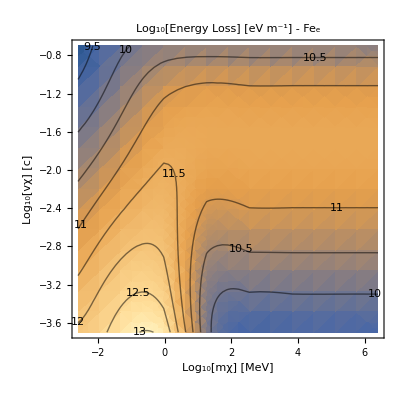

```mathematica
EnergyLoss`PlotEL[FeELOutputDictSIEnhancedTest,"Fe_e"]
```

```mathematica
Log10[("vF")/("c")/.FeELOutputDictSIEnhanced[["fitparams"]]]
```

{-2.25085,-2.16217,-2.04363,-1.7555,-1.05023,-0.388879}

```mathematica
Log10[("ℏ""ωp")/("JpereV")/.FeELOutputDictSIEnhanced[["fitparams"]]]
```

{1.07836,1.21138,1.38919,1.82139,2.87928,3.87131}

So transition happens around the plasmon energy - weight no it doesn’t this is eV

```mathematica
Log10[("ℏ""ωp")/("JpereV")/.FeELOutputDictSIEnhanced[["fitparams"]]]
```

#### Run SiO2

```mathematica
("β")^-1/("kB")/.SiO2Totalparams
```

{290.,290.}

```mathematica
SiO2ELOutputDictSIEnhanced = EnergyLossTableAndInterFITTotalParamsEnhanced[{2.5 10^3,2.5 10^12} ("JpereV")/("c")^2/.SIConstRepl,{2 10^-4,2 10^-1} "c" /.SIConstRepl,<|"mχ"->8,"vχ"->4|>,SiO2Totalparams,True,"SiO2ELOutputDictSIEnhanced"]
```

1 of 32

For mχ = 4.45×10^-33 , vχ = 60000
L:	0.000175393 
Prefactor:	2.08918×10^15
dEdr:	3.66428×10^11

$Aborted

```mathematica
SiO2ELOutputDictSIEnhanced = EnergyLossTableAndInterFITTotalParamsEnhanced[{2.5 10^3,2.5 10^12} ("JpereV")/("c")^2/.SIConstRepl,{2 10^-4,2 10^-1} "c" /.SIConstRepl,<|"mχ"->8,"vχ"->4|>,SiO2Totalparams,True,"SiO2ELOutputDictSIEnhanced"]
```

1 of 32

For mχ = 4.45×10^-33 , vχ = 60000
L:	0.000175393 
Prefactor:	2.08918×10^15
dEdr:	3.66428×10^11

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {3559.6}. NIntegrate obtained 0.00006384 and 2.53169×10^-6 for the integral and error estimates.

For mχ = 4.45×10^-33 , vχ = 60000
L:	0.00006384 
Prefactor:	2.77438×10^15
dEdr:	1.77116×10^11

dEdr total: 5.43545×10^11

2 of 32

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {3559.6}. NIntegrate obtained 0.001771 and 0.0000717928 for the integral and error estimates.

For mχ = 4.45×10^-33 , vχ = 600000
L:	0.001771 
Prefactor:	2.08918×10^13
dEdr:	3.69994×10^10

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {3559.6}. NIntegrate obtained 0.000631085 and 0.0000248038 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

For mχ = 4.45×10^-33 , vχ = 600000
L:	0.000631085 
Prefactor:	2.77438×10^13
dEdr:	1.75087×10^10

dEdr total: 5.45081×10^10

3 of 32

For mχ = 4.45×10^-33 , vχ = 6000000
L:	0.0172835 
Prefactor:	2.08918×10^11
dEdr:	3.61084×10^9

For mχ = 4.45×10^-33 , vχ = 6000000
L:	0.00660997 
Prefactor:	2.77438×10^11
dEdr:	1.83385×10^9

dEdr total: 5.44469×10^9

4 of 32

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.327776 
Prefactor:	2.08918×10^9
dEdr:	6.84785×10^8

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.079298 
Prefactor:	2.77438×10^9
dEdr:	2.20003×10^8

dEdr total: 9.04787×10^8

5 of 32

For mχ = 8.5916×10^-32 , vχ = 60000
L:	0.000797277 
Prefactor:	2.08918×10^15
dEdr:	1.66566×10^12

For mχ = 8.5916×10^-32 , vχ = 60000
L:	0.000305998 
Prefactor:	2.77438×10^15
dEdr:	8.48955×10^11

dEdr total: 2.51461×10^12

6 of 32

For mχ = 8.5916×10^-32 , vχ = 600000
L:	0.00796714 
Prefactor:	2.08918×10^13
dEdr:	1.66448×10^11

For mχ = 8.5916×10^-32 , vχ = 600000
L:	0.00305899 
Prefactor:	2.77438×10^13
dEdr:	8.4868×10^10

dEdr total: 2.51316×10^11

7 of 32

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.076435 
Prefactor:	2.08918×10^11
dEdr:	1.59687×10^10

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.0297862 
Prefactor:	2.77438×10^11
dEdr:	8.26381×10^9

dEdr total: 2.42325×10^10

8 of 32

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	0.961386 
Prefactor:	2.08918×10^9
dEdr:	2.00851×10^9

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	0.454893 
Prefactor:	2.77438×10^9
dEdr:	1.26205×10^9

dEdr total: 3.27056×10^9

9 of 32

For mχ = 1.65878×10^-30 , vχ = 60000
L:	0.000992502 
Prefactor:	2.08918×10^15
dEdr:	2.07352×10^12

For mχ = 1.65878×10^-30 , vχ = 60000
L:	0.000394726 
Prefactor:	2.77438×10^15
dEdr:	1.09512×10^12

dEdr total: 3.16864×10^12

10 of 32

For mχ = 1.65878×10^-30 , vχ = 600000
L:	0.0107805 
Prefactor:	2.08918×10^13
dEdr:	2.25224×10^11

For mχ = 1.65878×10^-30 , vχ = 600000
L:	0.00406926 
Prefactor:	2.77438×10^13
dEdr:	1.12897×10^11

dEdr total: 3.3812×10^11

11 of 32

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.468181 
Prefactor:	2.08918×10^11
dEdr:	9.78116×10^10

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.144233 
Prefactor:	2.77438×10^11
dEdr:	4.00158×10^10

dEdr total: 1.37827×10^11

12 of 32

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	1.45001 
Prefactor:	2.08918×10^9
dEdr:	3.02933×10^9

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	0.74311 
Prefactor:	2.77438×10^9
dEdr:	2.06167×10^9

dEdr total: 5.091×10^9

13 of 32

For mχ = 3.2026×10^-29 , vχ = 60000
L:	2.97971×10^-6 
Prefactor:	2.08918×10^15
dEdr:	6.22515×10^9

For mχ = 3.2026×10^-29 , vχ = 60000
L:	1.07087×10^-6 
Prefactor:	2.77438×10^15
dEdr:	2.97099×10^9

dEdr total: 9.19613×10^9

14 of 32

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.00125824 
Prefactor:	2.08918×10^13
dEdr:	2.62869×10^10

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.000214061 
Prefactor:	2.77438×10^13
dEdr:	5.93885×10^9

dEdr total: 3.22257×10^10

15 of 32

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.477385 
Prefactor:	2.08918×10^11
dEdr:	9.97344×10^10

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.147334 
Prefactor:	2.77438×10^11
dEdr:	4.08761×10^10

dEdr total: 1.4061×10^11

16 of 32

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	1.45363 
Prefactor:	2.08918×10^9
dEdr:	3.03689×10^9

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	0.745309 
Prefactor:	2.77438×10^9
dEdr:	2.06777×10^9

dEdr total: 5.10466×10^9

17 of 32

For mχ = 6.18325×10^-28 , vχ = 60000
L:	1.27123×10^-6 
Prefactor:	2.08918×10^15
dEdr:	2.65582×10^9

For mχ = 6.18325×10^-28 , vχ = 60000
L:	2.16379×10^-7 
Prefactor:	2.77438×10^15
dEdr:	6.00318×10^8

dEdr total: 3.25614×10^9

18 of 32

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.0013328 
Prefactor:	2.08918×10^13
dEdr:	2.78447×10^10

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.000229303 
Prefactor:	2.77438×10^13
dEdr:	6.36173×10^9

dEdr total: 3.42064×10^10

19 of 32

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.479441 
Prefactor:	2.08918×10^11
dEdr:	1.00164×10^11

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.148592 
Prefactor:	2.77438×10^11
dEdr:	4.12251×10^10

dEdr total: 1.41389×10^11

20 of 32

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	1.4554 
Prefactor:	2.08918×10^9
dEdr:	3.0406×10^9

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	0.746355 
Prefactor:	2.77438×10^9
dEdr:	2.07067×10^9

dEdr total: 5.11127×10^9

21 of 32

For mχ = 1.1938×10^-26 , vχ = 60000
L:	1.32068×10^-6 
Prefactor:	2.08918×10^15
dEdr:	2.75914×10^9

For mχ = 1.1938×10^-26 , vχ = 60000
L:	2.28052×10^-7 
Prefactor:	2.77438×10^15
dEdr:	6.32703×10^8

dEdr total: 3.39184×10^9

22 of 32

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.00133819 
Prefactor:	2.08918×10^13
dEdr:	2.79573×10^10

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.000230744 
Prefactor:	2.77438×10^13
dEdr:	6.40172×10^9

dEdr total: 3.4359×10^10

23 of 32

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.479552 
Prefactor:	2.08918×10^11
dEdr:	1.00187×10^11

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.14866 
Prefactor:	2.77438×10^11
dEdr:	4.1244×10^10

dEdr total: 1.41431×10^11

24 of 32

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	1.4555 
Prefactor:	2.08918×10^9
dEdr:	3.0408×10^9

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	0.746411 
Prefactor:	2.77438×10^9
dEdr:	2.07083×10^9

dEdr total: 5.11163×10^9

25 of 32

For mχ = 2.30487×10^-25 , vχ = 60000
L:	1.32366×10^-6 
Prefactor:	2.08918×10^15
dEdr:	2.76537×10^9

For mχ = 2.30487×10^-25 , vχ = 60000
L:	2.28838×10^-7 
Prefactor:	2.77438×10^15
dEdr:	6.34883×10^8

dEdr total: 3.40025×10^9

26 of 32

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.00133847 
Prefactor:	2.08918×10^13
dEdr:	2.79632×10^10

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.000230821 
Prefactor:	2.77438×10^13
dEdr:	6.40384×10^9

dEdr total: 3.4367×10^10

27 of 32

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.479557 
Prefactor:	2.08918×10^11
dEdr:	1.00188×10^11

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.148664 
Prefactor:	2.77438×10^11
dEdr:	4.1245×10^10

dEdr total: 1.41433×10^11

28 of 32

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	1.4555 
Prefactor:	2.08918×10^9
dEdr:	3.04081×10^9

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	0.746414 
Prefactor:	2.77438×10^9
dEdr:	2.07084×10^9

dEdr total: 5.11165×10^9

29 of 32

For mχ = 4.45×10^-24 , vχ = 60000
L:	1.32382×10^-6 
Prefactor:	2.08918×10^15
dEdr:	2.76569×10^9

For mχ = 4.45×10^-24 , vχ = 60000
L:	2.28879×10^-7 
Prefactor:	2.77438×10^15
dEdr:	6.34997×10^8

dEdr total: 3.40069×10^9

30 of 32

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.00133849 
Prefactor:	2.08918×10^13
dEdr:	2.79635×10^10

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.000230825 
Prefactor:	2.77438×10^13
dEdr:	6.40395×10^9

dEdr total: 3.43674×10^10

31 of 32

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.479558 
Prefactor:	2.08918×10^11
dEdr:	1.00188×10^11

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.148664 
Prefactor:	2.77438×10^11
dEdr:	4.1245×10^10

dEdr total: 1.41433×10^11

32 of 32

For mχ = 4.45×10^-24 , vχ = 60000000
L:	1.4555 
Prefactor:	2.08918×10^9
dEdr:	3.04081×10^9

For mχ = 4.45×10^-24 , vχ = 60000000
L:	0.746414 
Prefactor:	2.77438×10^9
dEdr:	2.07084×10^9

dEdr total: 5.11165×10^9

<|f→InterpolatingFunction[…],mχMesh→{{4.45×10^-33,4.45×10^-33,4.45×10^-33,4.45×10^-33},{8.5916×10^-32,8.5916×10^-32,8.5916×10^-32,8.5916×10^-32},{1.65878×10^-30,1.65878×10^-30,1.65878×10^-30,1.65878×10^-30},{3.2026×10^-29,3.2026×10^-29,3.2026×10^-29,3.2026×10^-29},{6.18325×10^-28,6.18325×10^-28,6.18325×10^-28,6.18325×10^-28},{1.1938×10^-26,1.1938×10^-26,1.1938×10^-26,1.1938×10^-26},{2.30487×10^-25,2.30487×10^-25,2.30487×10^-25,2.30487×10^-25},{4.45×10^-24,4.45×10^-24,4.45×10^-24,4.45×10^-24}},vχMesh→{{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000}},EnergyLossMesh→{{5.43545×10^11,5.45081×10^10,5.44469×10^9,9.04787×10^8},{2.51461×10^12,2.51316×10^11,2.42325×10^10,3.27056×10^9},{3.16864×10^12,3.3812×10^11,1.37827×10^11,5.091×10^9},{9.19613×10^9,3.22257×10^10,1.4061×10^11,5.10466×10^9},{3.25614×10^9,3.42064×10^10,1.41389×10^11,5.11127×10^9},{3.39184×10^9,3.4359×10^10,1.41431×10^11,5.11163×10^9},{3.40025×10^9,3.4367×10^10,1.41433×10^11,5.11165×10^9},{3.40069×10^9,3.43674×10^10,1.41433×10^11,5.11165×10^9}},fitparams→{{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.07027×10^29,qF→2.2927×10^10,vF→2.65511×10^6,μ→3.21109×10^-18,ωp→3.60151×10^16,α→1/137,χ→0.512371,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→801.791,nI→5.08784×10^28,Z→8,M→9.27329×10^-26,EF→3.21109×10^-18,ωi→3.60151×10^16,νi→2.11534×10^16,Ai→0.552697,ωedgei→0},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→2.0121×10^30,qF→3.90562×10^10,vF→4.52297×10^6,μ→9.3183×10^-18,ωp→8.0075×10^16,α→1/137,χ→0.392567,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→2326.72,nI→2.51512×10^29,Z→8,M→9.27329×10^-26,EF→9.3183×10^-18,ωi→8.0075×10^16,νi→6.06034×10^16,Ai→0.0871584,ωedgei→0}},fname→SiO2ELOutputDictSIEnhanced,kinlist→<|mχ→{4.45×10^-33,8.5916×10^-32,1.65878×10^-30,3.2026×10^-29,6.18325×10^-28,1.1938×10^-26,2.30487×10^-25,4.45×10^-24},vχ→{60000,600000,6000000,60000000}|>,meshdims→<|mχ→8,vχ→4|>,timesMesh→{{242.045,439.336,423.277,464.717},{10.8898,10.3367,14.9445,83.4077},{11.1538,12.1486,25.7176,223.783},{13.6816,17.5637,19.0839,139.819},{30.42,12.5462,17.9399,106.281},{22.4367,10.8751,17.0468,105.265},{25.1557,10.9617,17.0969,114.078},{23.1409,10.1744,17.4177,113.144}},totalTime→2805.89|>

#### Plot SiO2

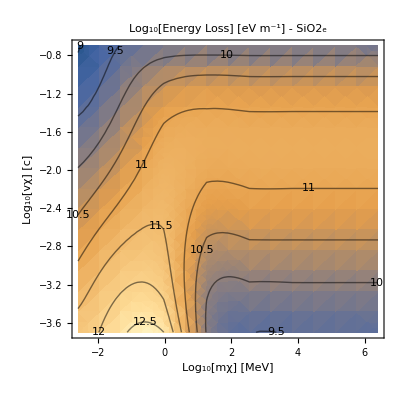

```mathematica
EnergyLoss`PlotEL[SiO2ELOutputDictSIEnhanced,"SiO2_e"]
```

```mathematica
Log10[("vF")/("c")/.SiO2ELOutputDictSIEnhanced[["fitparams"]]]
```

{-2.05304,-1.8217}

#### Run MgO

```mathematica
MgOELOutputDictSIEnhanced = EnergyLossTableAndInterFITTotalParamsEnhanced[{2.5 10^3,2.5 10^12} ("JpereV")/("c")^2/.SIConstRepl,{2 10^-4,2 10^-1} "c" /.SIConstRepl,<|"mχ"->8,"vχ"->4|>,MgOTotalparams,True,"MgOELOutputDictSIEnhanced"]
```

1 of 32

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1987.19}. NIntegrate obtained 0.000337559 and 4.38616×10^-6 for the integral and error estimates.

For mχ = 4.45×10^-33 , vχ = 60000
L:	0.000337559 
Prefactor:	3.99192×10^13
dEdr:	1.34751×10^10

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1983.01}. NIntegrate obtained 0.000208341 and 1.08951×10^-6 for the integral and error estimates.

For mχ = 4.45×10^-33 , vχ = 60000
L:	0.000208341 
Prefactor:	5.73915×10^14
dEdr:	1.1957×10^11

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {3559.6}. NIntegrate obtained 0.000182741 and 4.01308×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

For mχ = 4.45×10^-33 , vχ = 60000
L:	0.000182741 
Prefactor:	4.00973×10^14
dEdr:	7.32741×10^10

For mχ = 4.45×10^-33 , vχ = 60000
L:	0.0000668434 
Prefactor:	1.00279×10^16
dEdr:	6.703×10^11

dEdr total: 8.76619×10^11

2 of 32

For mχ = 4.45×10^-33 , vχ = 600000
L:	0.00337213 
Prefactor:	3.99192×10^11
dEdr:	1.34613×10^9

For mχ = 4.45×10^-33 , vχ = 600000
L:	0.00214005 
Prefactor:	5.73915×10^12
dEdr:	1.22821×10^10

For mχ = 4.45×10^-33 , vχ = 600000
L:	0.00183626 
Prefactor:	4.00973×10^12
dEdr:	7.36293×10^9

For mχ = 4.45×10^-33 , vχ = 600000
L:	0.000596438 
Prefactor:	1.00279×10^14
dEdr:	5.98103×10^10

dEdr total: 8.08015×10^10

3 of 32

For mχ = 4.45×10^-33 , vχ = 6000000
L:	0.0339014 
Prefactor:	3.99192×10^9
dEdr:	1.35332×10^8

For mχ = 4.45×10^-33 , vχ = 6000000
L:	0.0208949 
Prefactor:	5.73915×10^10
dEdr:	1.19919×10^9

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

For mχ = 4.45×10^-33 , vχ = 6000000
L:	0.018411 
Prefactor:	4.00973×10^10
dEdr:	7.38233×10^8

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

For mχ = 4.45×10^-33 , vχ = 6000000
L:	0.006315 
Prefactor:	1.00279×10^12
dEdr:	6.33263×10^9

dEdr total: 8.40538×10^9

4 of 32

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.688955 
Prefactor:	3.99192×10^7
dEdr:	2.75026×10^7

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.420291 
Prefactor:	5.73915×10^8
dEdr:	2.41211×10^8

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.370221 
Prefactor:	4.00973×10^8
dEdr:	1.48449×10^8

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.0834964 
Prefactor:	1.00279×10^10
dEdr:	8.37294×10^8

dEdr total: 1.25446×10^9

5 of 32

For mχ = 8.5916×10^-32 , vχ = 60000
L:	0.00154969 
Prefactor:	3.99192×10^13
dEdr:	6.18623×10^10

For mχ = 8.5916×10^-32 , vχ = 60000
L:	0.000950025 
Prefactor:	5.73915×10^14
dEdr:	5.45234×10^11

For mχ = 8.5916×10^-32 , vχ = 60000
L:	0.000848748 
Prefactor:	4.00973×10^14
dEdr:	3.40325×10^11

For mχ = 8.5916×10^-32 , vχ = 60000
L:	0.000302277 
Prefactor:	1.00279×10^16
dEdr:	3.03121×10^12

dEdr total: 3.97863×10^12

6 of 32

For mχ = 8.5916×10^-32 , vχ = 600000
L:	0.0154786 
Prefactor:	3.99192×10^11
dEdr:	6.17895×10^9

For mχ = 8.5916×10^-32 , vχ = 600000
L:	0.00949283 
Prefactor:	5.73915×10^12
dEdr:	5.44808×10^10

For mχ = 8.5916×10^-32 , vχ = 600000
L:	0.00848144 
Prefactor:	4.00973×10^12
dEdr:	3.40083×10^10

For mχ = 8.5916×10^-32 , vχ = 600000
L:	0.00302172 
Prefactor:	1.00279×10^14
dEdr:	3.03015×10^11

dEdr total: 3.97683×10^11

7 of 32

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.14523 
Prefactor:	3.99192×10^9
dEdr:	5.79748×10^8

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.0894217 
Prefactor:	5.73915×10^10
dEdr:	5.13205×10^9

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.080161 
Prefactor:	4.00973×10^10
dEdr:	3.21424×10^9

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.029554 
Prefactor:	1.00279×10^12
dEdr:	2.96365×10^10

dEdr total: 3.85625×10^10

8 of 32

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	1.55492 
Prefactor:	3.99192×10^7
dEdr:	6.20714×10^7

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	1.07773 
Prefactor:	5.73915×10^8
dEdr:	6.18526×10^8

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	0.989519 
Prefactor:	4.00973×10^8
dEdr:	3.9677×10^8

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	0.455491 
Prefactor:	1.00279×10^10
dEdr:	4.56763×10^9

dEdr total: 5.64499×10^9

9 of 32

For mχ = 1.65878×10^-30 , vχ = 60000
L:	0.00167282 
Prefactor:	3.99192×10^13
dEdr:	6.67777×10^10

For mχ = 1.65878×10^-30 , vχ = 60000
L:	0.00102198 
Prefactor:	5.73915×10^14
dEdr:	5.86528×10^11

For mχ = 1.65878×10^-30 , vχ = 60000
L:	0.000910984 
Prefactor:	4.00973×10^14
dEdr:	3.6528×10^11

For mχ = 1.65878×10^-30 , vχ = 60000
L:	0.000477238 
Prefactor:	1.00279×10^16
dEdr:	4.7857×10^12

dEdr total: 5.80429×10^12

10 of 32

For mχ = 1.65878×10^-30 , vχ = 600000
L:	0.0195732 
Prefactor:	3.99192×10^11
dEdr:	7.81349×10^9

For mχ = 1.65878×10^-30 , vχ = 600000
L:	0.0112008 
Prefactor:	5.73915×10^12
dEdr:	6.4283×10^10

For mχ = 1.65878×10^-30 , vχ = 600000
L:	0.00987762 
Prefactor:	4.00973×10^12
dEdr:	3.96066×10^10

For mχ = 1.65878×10^-30 , vχ = 600000
L:	0.00491014 
Prefactor:	1.00279×10^14
dEdr:	4.92384×10^11

dEdr total: 6.04087×10^11

11 of 32

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.889273 
Prefactor:	3.99192×10^9
dEdr:	3.54991×10^9

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.564989 
Prefactor:	5.73915×10^10
dEdr:	3.24256×10^10

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.505175 
Prefactor:	4.00973×10^10
dEdr:	2.02562×10^10

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.148432 
Prefactor:	1.00279×10^12
dEdr:	1.48846×10^11

dEdr total: 2.05078×10^11

12 of 32

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	2.23428 
Prefactor:	3.99192×10^7
dEdr:	8.91907×10^7

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	1.58689 
Prefactor:	5.73915×10^8
dEdr:	9.10741×10^8

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	1.46595 
Prefactor:	4.00973×10^8
dEdr:	5.87806×10^8

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	0.766219 
Prefactor:	1.00279×10^10
dEdr:	7.68358×10^9

dEdr total: 9.27131×10^9

13 of 32

For mχ = 3.2026×10^-29 , vχ = 60000
L:	5.18221×10^-6 
Prefactor:	3.99192×10^13
dEdr:	2.0687×10^8

For mχ = 3.2026×10^-29 , vχ = 60000
L:	2.73418×10^-6 
Prefactor:	5.73915×10^14
dEdr:	1.56919×10^9

For mχ = 3.2026×10^-29 , vχ = 60000
L:	2.37642×10^-6 
Prefactor:	4.00973×10^14
dEdr:	9.52881×10^8

For mχ = 3.2026×10^-29 , vχ = 60000
L:	1.52113×10^-6 
Prefactor:	1.00279×10^16
dEdr:	1.52537×10^10

dEdr total: 1.79827×10^10

14 of 32

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.00326769 
Prefactor:	3.99192×10^11
dEdr:	1.30444×10^9

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.00122198 
Prefactor:	5.73915×10^12
dEdr:	7.01313×10^9

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.000972574 
Prefactor:	4.00973×10^12
dEdr:	3.89976×10^9

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.000354509 
Prefactor:	1.00279×10^14
dEdr:	3.55499×10^10

dEdr total: 4.77672×10^10

15 of 32

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.898256 
Prefactor:	3.99192×10^9
dEdr:	3.58577×10^9

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.574123 
Prefactor:	5.73915×10^10
dEdr:	3.29498×10^10

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.514572 
Prefactor:	4.00973×10^10
dEdr:	2.0633×10^10

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.147888 
Prefactor:	1.00279×10^12
dEdr:	1.48301×10^11

dEdr total: 2.0547×10^11

16 of 32

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	2.23944 
Prefactor:	3.99192×10^7
dEdr:	8.93967×10^7

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	1.59063 
Prefactor:	5.73915×10^8
dEdr:	9.1289×10^8

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	1.46945 
Prefactor:	4.00973×10^8
dEdr:	5.89211×10^8

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	0.768635 
Prefactor:	1.00279×10^10
dEdr:	7.70781×10^9

dEdr total: 9.2993×10^9

17 of 32

For mχ = 6.18325×10^-28 , vχ = 60000
L:	3.22165×10^-6 
Prefactor:	3.99192×10^13
dEdr:	1.28606×10^8

For mχ = 6.18325×10^-28 , vχ = 60000
L:	1.22057×10^-6 
Prefactor:	5.73915×10^14
dEdr:	7.00503×10^8

For mχ = 6.18325×10^-28 , vχ = 60000
L:	9.73437×10^-7 
Prefactor:	4.00973×10^14
dEdr:	3.90322×10^8

For mχ = 6.18325×10^-28 , vχ = 60000
L:	3.61604×10^-7 
Prefactor:	1.00279×10^16
dEdr:	3.62614×10^9

dEdr total: 4.84557×10^9

18 of 32

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.00343064 
Prefactor:	3.99192×10^11
dEdr:	1.36948×10^9

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.0012945 
Prefactor:	5.73915×10^12
dEdr:	7.42932×10^9

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.00103241 
Prefactor:	4.00973×10^12
dEdr:	4.1397×10^9

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.000378692 
Prefactor:	1.00279×10^14
dEdr:	3.79749×10^10

dEdr total: 5.09134×10^10

19 of 32

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.900914 
Prefactor:	3.99192×10^9
dEdr:	3.59638×10^9

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.576212 
Prefactor:	5.73915×10^10
dEdr:	3.30697×10^10

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.516556 
Prefactor:	4.00973×10^10
dEdr:	2.07125×10^10

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.149062 
Prefactor:	1.00279×10^12
dEdr:	1.49478×10^11

dEdr total: 2.06857×10^11

20 of 32

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	2.24101 
Prefactor:	3.99192×10^7
dEdr:	8.94595×10^7

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	1.59248 
Prefactor:	5.73915×10^8
dEdr:	9.13951×10^8

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	1.47118 
Prefactor:	4.00973×10^8
dEdr:	5.89905×10^8

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	0.769763 
Prefactor:	1.00279×10^10
dEdr:	7.71911×10^9

dEdr total: 9.31243×10^9

21 of 32

For mχ = 1.1938×10^-26 , vχ = 60000
L:	3.32264×10^-6 
Prefactor:	3.99192×10^13
dEdr:	1.32637×10^8

For mχ = 1.1938×10^-26 , vχ = 60000
L:	1.26762×10^-6 
Prefactor:	5.73915×10^14
dEdr:	7.27504×10^8

For mχ = 1.1938×10^-26 , vχ = 60000
L:	1.01275×10^-6 
Prefactor:	4.00973×10^14
dEdr:	4.06084×10^8

For mχ = 1.1938×10^-26 , vχ = 60000
L:	3.79569×10^-7 
Prefactor:	1.00279×10^16
dEdr:	3.80629×10^9

dEdr total: 5.07251×10^9

22 of 32

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.00344154 
Prefactor:	3.99192×10^11
dEdr:	1.37384×10^9

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.00129973 
Prefactor:	5.73915×10^12
dEdr:	7.45935×10^9

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.00103683 
Prefactor:	4.00973×10^12
dEdr:	4.15741×10^9

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.000380819 
Prefactor:	1.00279×10^14
dEdr:	3.81882×10^10

dEdr total: 5.11788×10^10

23 of 32

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.901058 
Prefactor:	3.99192×10^9
dEdr:	3.59695×10^9

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.576324 
Prefactor:	5.73915×10^10
dEdr:	3.30761×10^10

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.516663 
Prefactor:	4.00973×10^10
dEdr:	2.07168×10^10

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.149126 
Prefactor:	1.00279×10^12
dEdr:	1.49543×10^11

dEdr total: 2.06932×10^11

24 of 32

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	2.24204 
Prefactor:	3.99192×10^7
dEdr:	8.95005×10^7

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	1.59259 
Prefactor:	5.73915×10^8
dEdr:	9.14009×10^8

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	1.47128 
Prefactor:	4.00973×10^8
dEdr:	5.89942×10^8

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	0.769823 
Prefactor:	1.00279×10^10
dEdr:	7.71972×10^9

dEdr total: 9.31318×10^9

25 of 32

For mχ = 2.30487×10^-25 , vχ = 60000
L:	3.32846×10^-6 
Prefactor:	3.99192×10^13
dEdr:	1.3287×10^8

For mχ = 2.30487×10^-25 , vχ = 60000
L:	1.27043×10^-6 
Prefactor:	5.73915×10^14
dEdr:	7.29119×10^8

For mχ = 2.30487×10^-25 , vχ = 60000
L:	1.01512×10^-6 
Prefactor:	4.00973×10^14
dEdr:	4.07037×10^8

For mχ = 2.30487×10^-25 , vχ = 60000
L:	3.8075×10^-7 
Prefactor:	1.00279×10^16
dEdr:	3.81813×10^9

dEdr total: 5.08715×10^9

26 of 32

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.00344211 
Prefactor:	3.99192×10^11
dEdr:	1.37406×10^9

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.00130001 
Prefactor:	5.73915×10^12
dEdr:	7.46093×10^9

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.00103706 
Prefactor:	4.00973×10^12
dEdr:	4.15834×10^9

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.000380932 
Prefactor:	1.00279×10^14
dEdr:	3.81995×10^10

dEdr total: 5.11929×10^10

27 of 32

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.901065 
Prefactor:	3.99192×10^9
dEdr:	3.59698×10^9

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.57633 
Prefactor:	5.73915×10^10
dEdr:	3.30765×10^10

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.516669 
Prefactor:	4.00973×10^10
dEdr:	2.0717×10^10

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.14913 
Prefactor:	1.00279×10^12
dEdr:	1.49546×10^11

dEdr total: 2.06936×10^11

28 of 32

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	2.24184 
Prefactor:	3.99192×10^7
dEdr:	8.94926×10^7

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	1.59259 
Prefactor:	5.73915×10^8
dEdr:	9.14012×10^8

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	1.47128 
Prefactor:	4.00973×10^8
dEdr:	5.89945×10^8

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	0.769827 
Prefactor:	1.00279×10^10
dEdr:	7.71976×10^9

dEdr total: 9.31321×10^9

29 of 32

For mχ = 4.45×10^-24 , vχ = 60000
L:	3.32876×10^-6 
Prefactor:	3.99192×10^13
dEdr:	1.32882×10^8

For mχ = 4.45×10^-24 , vχ = 60000
L:	1.27058×10^-6 
Prefactor:	5.73915×10^14
dEdr:	7.29204×10^8

For mχ = 4.45×10^-24 , vχ = 60000
L:	1.01525×10^-6 
Prefactor:	4.00973×10^14
dEdr:	4.07086×10^8

For mχ = 4.45×10^-24 , vχ = 60000
L:	3.80812×10^-7 
Prefactor:	1.00279×10^16
dEdr:	3.81875×10^9

dEdr total: 5.08792×10^9

30 of 32

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.00344214 
Prefactor:	3.99192×10^11
dEdr:	1.37408×10^9

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.00130002 
Prefactor:	5.73915×10^12
dEdr:	7.46101×10^9

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.00103707 
Prefactor:	4.00973×10^12
dEdr:	4.15839×10^9

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.000380938 
Prefactor:	1.00279×10^14
dEdr:	3.82001×10^10

dEdr total: 5.11936×10^10

31 of 32

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.901066 
Prefactor:	3.99192×10^9
dEdr:	3.59698×10^9

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.57633 
Prefactor:	5.73915×10^10
dEdr:	3.30765×10^10

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.516669 
Prefactor:	4.00973×10^10
dEdr:	2.0717×10^10

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.14913 
Prefactor:	1.00279×10^12
dEdr:	1.49546×10^11

dEdr total: 2.06937×10^11

32 of 32

For mχ = 4.45×10^-24 , vχ = 60000000
L:	2.24184 
Prefactor:	3.99192×10^7
dEdr:	8.94926×10^7

For mχ = 4.45×10^-24 , vχ = 60000000
L:	1.59259 
Prefactor:	5.73915×10^8
dEdr:	9.14012×10^8

For mχ = 4.45×10^-24 , vχ = 60000000
L:	1.47128 
Prefactor:	4.00973×10^8
dEdr:	5.89944×10^8

For mχ = 4.45×10^-24 , vχ = 60000000
L:	0.769827 
Prefactor:	1.00279×10^10
dEdr:	7.71976×10^9

dEdr total: 9.31321×10^9

<|f→InterpolatingFunction[…],mχMesh→{{4.45×10^-33,4.45×10^-33,4.45×10^-33,4.45×10^-33},{8.5916×10^-32,8.5916×10^-32,8.5916×10^-32,8.5916×10^-32},{1.65878×10^-30,1.65878×10^-30,1.65878×10^-30,1.65878×10^-30},{3.2026×10^-29,3.2026×10^-29,3.2026×10^-29,3.2026×10^-29},{6.18325×10^-28,6.18325×10^-28,6.18325×10^-28,6.18325×10^-28},{1.1938×10^-26,1.1938×10^-26,1.1938×10^-26,1.1938×10^-26},{2.30487×10^-25,2.30487×10^-25,2.30487×10^-25,2.30487×10^-25},{4.45×10^-24,4.45×10^-24,4.45×10^-24,4.45×10^-24}},vχMesh→{{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000}},EnergyLossMesh→{{8.76619×10^11,8.08015×10^10,8.40538×10^9,1.25446×10^9},{3.97863×10^12,3.97683×10^11,3.85625×10^10,5.64499×10^9},{5.80429×10^12,6.04087×10^11,2.05078×10^11,9.27131×10^9},{1.79827×10^10,4.77672×10^10,2.0547×10^11,9.2993×10^9},{4.84557×10^9,5.09134×10^10,2.06857×10^11,9.31243×10^9},{5.07251×10^9,5.11788×10^10,2.06932×10^11,9.31318×10^9},{5.08715×10^9,5.11929×10^10,2.06936×10^11,9.31321×10^9},{5.08792×10^9,5.11936×10^10,2.06937×10^11,9.31321×10^9}},fitparams→{{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→1.50385×10^29,qF→1.64516×10^10,vF→1.90521×10^6,μ→1.65338×10^-18,ωp→2.18914×10^16,α→1/137,χ→0.604859,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→412.839,nI→1.87981×10^28,Z→8,M→9.27329×10^-26,EF→1.65338×10^-18,ωi→2.18914×10^16,νi→4.25006×10^15,Ai→0.039834,ωedgei→0},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→3.58115×10^29,qF→2.19692×10^10,vF→2.54418×10^6,μ→2.94839×10^-18,ωp→3.37819×10^16,α→1/137,χ→0.523421,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→736.197,nI→4.47644×10^28,Z→8,M→9.27329×10^-26,EF→2.94839×10^-18,ωi→3.37819×10^16,νi→5.06751×10^15,Ai→0.180092,ωedgei→0},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.37351×10^29,qF→2.34828×10^10,vF→2.71947×10^6,μ→3.36866×10^-18,ωp→3.73325×10^16,α→1/137,χ→0.506271,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→841.135,nI→5.46689×10^28,Z→8,M→9.27329×10^-26,EF→3.36866×10^-18,ωi→3.73325×10^16,νi→5.23006×10^15,Ai→0.0963866,ωedgei→0},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→1.61838×10^30,qF→3.63218×10^10,vF→4.20631×10^6,μ→8.05919×10^-18,ωp→7.18146×10^16,α→1/137,χ→0.407075,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→2012.33,nI→2.02298×10^29,Z→8,M→9.27329×10^-26,EF→8.05919×10^-18,ωi→7.18146×10^16,νi→1.12397×10^17,Ai→0.421157,ωedgei→0}},fname→MgOELOutputDictSIEnhanced,kinlist→<|mχ→{4.45×10^-33,8.5916×10^-32,1.65878×10^-30,3.2026×10^-29,6.18325×10^-28,1.1938×10^-26,2.30487×10^-25,4.45×10^-24},vχ→{60000,600000,6000000,60000000}|>,meshdims→<|mχ→8,vχ→4|>,timesMesh→{{986.281,1532.73,1432.49,915.526},{23.9448,31.1745,55.902,264.427},{22.9495,32.4782,109.425,437.84},{37.8147,48.8602,77.9548,450.938},{69.0436,37.8296,77.926,380.519},{63.4725,33.6695,75.334,354.165},{63.3948,33.62,74.725,365.064},{61.6086,32.191,74.2328,363.928}},totalTime→8621.46|>

#### Plot MgO

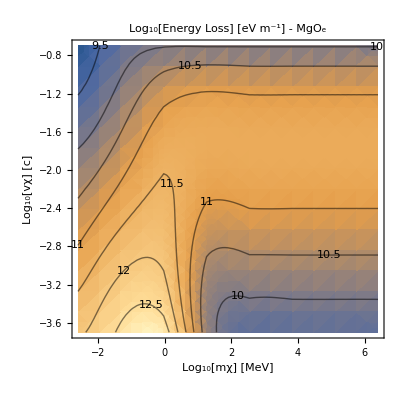

```mathematica
EnergyLoss`PlotEL[MgOELOutputDictSIEnhanced,"MgO_e"]
```

```mathematica
Log10[("vF")/("c")/.MgOELOutputDictSIEnhanced[["fitparams"]]]
```

{-2.19718,-2.07157,-2.04264,-1.85322}

### Find fraction of silicate energy loss below the band gap

Here we investigate the fraction of the contribution to the energy loss from part of the phase space below the band gap in the silicates, since our use of the optical data there is questionable. This is a check of our approximation.

bbg suffixes stand for below band gap

#### Run SiO2

```mathematica
(*ωbgSiO2 = 8.90 ("JpereV")/("ℏ")/.SIConstRepl
SiO2Totalparamsbbg = Table[Join[SiO2Totalparams[[i]],{"ωbg"->ωbgSiO2}],{i,Length[SiO2Totalparams]}]*)
```

1.35145×10^16

{{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.07027×10^29,qF→2.2927×10^10,vF→2.65511×10^6,μ→3.21109×10^-18,ωp→3.60151×10^16,α→1/137,χ→0.512371,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→801.791,nI→5.08784×10^28,Z→8,M→9.27329×10^-26,EF→3.21109×10^-18,ωi→3.60151×10^16,νi→2.11534×10^16,Ai→0.552697,ωedgei→0,ωbg→1.35145×10^16},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→2.0121×10^30,qF→3.90562×10^10,vF→4.52297×10^6,μ→9.3183×10^-18,ωp→8.0075×10^16,α→1/137,χ→0.392567,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→2326.72,nI→2.51512×10^29,Z→8,M→9.27329×10^-26,EF→9.3183×10^-18,ωi→8.0075×10^16,νi→6.06034×10^16,Ai→0.0871584,ωedgei→0,ωbg→1.35145×10^16}}

```mathematica
(*EnergyLossMSIFitEnhanced[2.5 10^12("JpereV")/("c")^2/.SIConstRepl,2 10^-1"c" /.SIConstRepl,SiO2Totalparamsbbg[[1]]]*)
```

For mχ = 4.45×10^-24 , vχ = 60000000
L:	1.94132 
Prefactor:	2.08918×10^9
dEdr:	4.05577×10^9

<|mχ→4.45×10^-24,vχ→60000000,fitparams→{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.07027×10^29,qF→2.2927×10^10,vF→2.65511×10^6,μ→3.21109×10^-18,ωp→3.60151×10^16,α→1/137,χ→0.512371,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→801.791,nI→5.08784×10^28,Z→8,M→9.27329×10^-26,EF→3.21109×10^-18,ωi→3.60151×10^16,νi→2.11534×10^16,Ai→0.552697,ωedgei→0,ωbg→1.35145×10^16},L→1.94132,Prefactor→2.08918×10^9,dEdr→4.05577×10^9|>

```mathematica
(*EnergyLossMSIFitEnhanced[2.5 10^3("JpereV")/("c")^2/.SIConstRepl,2 10^-4"c" /.SIConstRepl,FeTotalparams[[1]]]*)
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1987.19}. NIntegrate obtained 0.000726932 and 6.96818×10^-6 for the integral and error estimates.

For mχ = 4.45×10^-33 , vχ = 60000
L:	0.000726932 
Prefactor:	1.28051×10^14
dEdr:	9.30847×10^10

<|mχ→4.45×10^-33,vχ→60000,fitparams→{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→1.038×10^29,qF→1.45392×10^10,vF→1.68373×10^6,μ→1.29132×10^-18,ωp→1.81874×10^16,α→1/137,χ→0.643411,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→322.436,nI→1.2975×10^28,Z→8,M→9.27329×10^-26,EF→1.29132×10^-18,ωi→1.81874×10^16,νi→1.75116×10^16,Ai→0.209474,ωedgei→6.04519×10^14},L→0.000726932,Prefactor→1.28051×10^14,dEdr→9.30847×10^10|>

```mathematica
(*EnergyLossMSIFitEnhanced[2.5 10^12("JpereV")/("c")^2/.SIConstRepl,2 10^-1"c" /.SIConstRepl,SiO2Totalparamsbbg[[1]]]*)
```

For mχ = 4.45×10^-24 , vχ = 60000000
L:	1.94132 
Prefactor:	2.08918×10^9
dEdr:	4.05577×10^9

<|mχ→4.45×10^-24,vχ→60000000,fitparams→{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.07027×10^29,qF→2.2927×10^10,vF→2.65511×10^6,μ→3.21109×10^-18,ωp→3.60151×10^16,α→1/137,χ→0.512371,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→801.791,nI→5.08784×10^28,Z→8,M→9.27329×10^-26,EF→3.21109×10^-18,ωi→3.60151×10^16,νi→2.11534×10^16,Ai→0.552697,ωedgei→0,ωbg→1.35145×10^16},L→1.94132,Prefactor→2.08918×10^9,dEdr→4.05577×10^9|>

```mathematica
(*EnergyLossMSIFitEnhanced[2.5 10^12("JpereV")/("c")^2/.SIConstRepl,2 10^-1"c" /.SIConstRepl,SiO2Totalparamsbbg[[1]]]*)
```

For mχ = 4.45×10^-24 , vχ = 60000000
L:	1.94132 
Prefactor:	2.08918×10^9
dEdr:	4.05577×10^9

<|mχ→4.45×10^-24,vχ→60000000,fitparams→{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.07027×10^29,qF→2.2927×10^10,vF→2.65511×10^6,μ→3.21109×10^-18,ωp→3.60151×10^16,α→1/137,χ→0.512371,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→801.791,nI→5.08784×10^28,Z→8,M→9.27329×10^-26,EF→3.21109×10^-18,ωi→3.60151×10^16,νi→2.11534×10^16,Ai→0.552697,ωedgei→0,ωbg→1.35145×10^16},L→1.94132,Prefactor→2.08918×10^9,dEdr→4.05577×10^9|>

```mathematica
(*EnergyLossMSIFitEnhanced[2.5 10^7("JpereV")/("c")^2/.SIConstRepl,2 10^-1"c" /.SIConstRepl,SiO2Totalparamsbbg[[1]]]*)
```

For mχ = 4.45×10^-29 , vχ = 60000000
L:	1.94138 
Prefactor:	2.08918×10^9
dEdr:	4.05589×10^9

<|mχ→4.45×10^-29,vχ→60000000,fitparams→{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.07027×10^29,qF→2.2927×10^10,vF→2.65511×10^6,μ→3.21109×10^-18,ωp→3.60151×10^16,α→1/137,χ→0.512371,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→801.791,nI→5.08784×10^28,Z→8,M→9.27329×10^-26,EF→3.21109×10^-18,ωi→3.60151×10^16,νi→2.11534×10^16,Ai→0.552697,ωedgei→0,ωbg→1.35145×10^16},L→1.94138,Prefactor→2.08918×10^9,dEdr→4.05589×10^9|>

```mathematica
(*EnergyLossMSIFitEnhanced[2.5 10^12("JpereV")/("c")^2/.SIConstRepl,2 10^-1"c" /.SIConstRepl,SiO2Totalparamsbbg[[1]]]*)
```

For mχ = 4.45×10^-24 , vχ = 60000000
L:	1.94132 
Prefactor:	2.08918×10^9
dEdr:	4.05577×10^9

<|mχ→4.45×10^-24,vχ→60000000,fitparams→{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.07027×10^29,qF→2.2927×10^10,vF→2.65511×10^6,μ→3.21109×10^-18,ωp→3.60151×10^16,α→1/137,χ→0.512371,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→801.791,nI→5.08784×10^28,Z→8,M→9.27329×10^-26,EF→3.21109×10^-18,ωi→3.60151×10^16,νi→2.11534×10^16,Ai→0.552697,ωedgei→0,ωbg→1.35145×10^16},L→1.94132,Prefactor→2.08918×10^9,dEdr→4.05577×10^9|>

```mathematica
(*EnergyLossMSIFitEnhanced[2.5 10^12("JpereV")/("c")^2/.SIConstRepl,2 10^-1"c" /.SIConstRepl,SiO2Totalparamsbbg[[1]]]*)
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.615183}. NIntegrate obtained 0.00496808 and 5.55222×10^-6 for the integral and error estimates.

For mχ = 4.45×10^-24 , vχ = 60000000
L:	0.00496808 
Prefactor:	2.08918×10^9
dEdr:	1.03792×10^7

<|mχ→4.45×10^-24,vχ→60000000,fitparams→{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.07027×10^29,qF→2.2927×10^10,vF→2.65511×10^6,μ→3.21109×10^-18,ωp→3.60151×10^16,α→1/137,χ→0.512371,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→801.791,nI→5.08784×10^28,Z→8,M→9.27329×10^-26,EF→3.21109×10^-18,ωi→3.60151×10^16,νi→2.11534×10^16,Ai→0.552697,ωedgei→0,ωbg→1.35145×10^16},L→0.00496808,Prefactor→2.08918×10^9,dEdr→1.03792×10^7|>

```mathematica
(*EnergyLossMSIFitEnhanced[2.5 10^12("JpereV")/("c")^2/.SIConstRepl,2 10^-1"c" /.SIConstRepl,ReplaceParams[SiO2Totalparamsbbg[[1]],10^20,"ωbg"]]*)
```

For mχ = 4.45×10^-24 , vχ = 60000000
L:	0.970659 
Prefactor:	2.08918×10^9
dEdr:	2.02788×10^9

<|mχ→4.45×10^-24,vχ→60000000,fitparams→{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.07027×10^29,qF→2.2927×10^10,vF→2.65511×10^6,μ→3.21109×10^-18,ωp→3.60151×10^16,α→1/137,χ→0.512371,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→801.791,nI→5.08784×10^28,Z→8,M→9.27329×10^-26,EF→3.21109×10^-18,ωi→3.60151×10^16,νi→2.11534×10^16,Ai→0.552697,ωedgei→0,ωbg→100000000000000000000},L→0.970659,Prefactor→2.08918×10^9,dEdr→2.02788×10^9|>

```mathematica
(*uMIntegralFitEnhanced[1.1,2.5 10^12("JpereV")/("c")^2/.SIConstRepl,2 10^-1"c" /.SIConstRepl,SiO2Totalparamsbbg[[1]]]*)
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

0.

```mathematica
(*uMIntegralFitEnhanced[0.1,2.5 10^12("JpereV")/("c")^2/.SIConstRepl,2 10^-1"c" /.SIConstRepl,SiO2Totalparamsbbg[[1]]]*)
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`u near {EnergyLoss`Private`u} = {1.14685}. NIntegrate obtained 0.101876 and 0.00187779 for the integral and error estimates.

0.101876

```mathematica
(*HeavisideTheta[(("ℏ""ωbg")/(z 4"EF")-Abs[u])/.SiO2Totalparamsbbg[[1]]]/.u->(0.1"c"/"vF"/.SiO2Totalparamsbbg[[1]])*)
```

HeavisideTheta[-11.299+0.111004/z]

```mathematica
(*0.1"c"/"vF"/.SiO2Totalparamsbbg[[1]]*)
```

11.299

```mathematica
(*SiO2ELOutputDictSIEnhancedbbg = EnergyLossTableAndInterFITTotalParamsEnhanced[{2.5 10^3,2.5 10^12} ("JpereV")/("c")^2/.SIConstRepl,{2 10^-4,2 10^-1} "c" /.SIConstRepl,<|"mχ"->8,"vχ"->4|>,SiO2Totalparamsbbg,True,"SiO2ELOutputDictSIEnhancedbbg"]*)
```

1 of 32

For mχ = 4.45×10^-33 , vχ = 60000
L:	0.000351525 
Prefactor:	2.08918×10^15
dEdr:	7.344×10^11

$Aborted

#### Plot SiO2

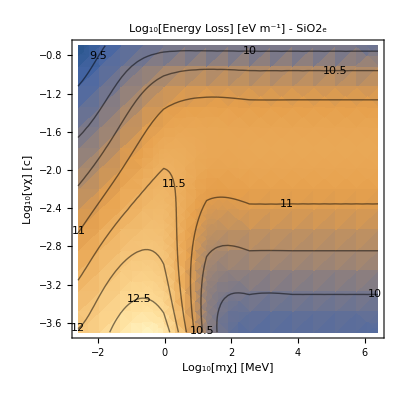

```mathematica
(*EnergyLoss`PlotEL[SiO2ELOutputDictSIEnhancedbbg,"SiO2_e"]*)
```

#### Run MgO

```mathematica
(*ωbgMgO = 7.77("JpereV")/("ℏ")/.SIConstRepl
MgOTotalparamsbbg = Table[Join[MgOTotalparams[[i]],{"ωbg"->ωbgMgO}],{i,Length[MgOTotalparams]}]*)
```

```mathematica
(*MgOELOutputDictSIEnhancedbbg = EnergyLossTableAndInterFITTotalParamsEnhanced[{2.5 10^3,2.5 10^12} ("JpereV")/("c")^2/.SIConstRepl,{2 10^-4,2 10^-1} "c" /.SIConstRepl,<|"mχ"->8,"vχ"->4|>,MgOTotalparamsbbg,True,"MgOELOutputDictSIEnhancedbbg"]*)
```

1 of 32

dEdr total: 0

2 of 32

dEdr total: 0

3 of 32

dEdr total: 0

4 of 32

dEdr total: 0

5 of 32

dEdr total: 0

6 of 32

dEdr total: 0

7 of 32

dEdr total: 0

8 of 32

dEdr total: 0

9 of 32

dEdr total: 0

10 of 32

dEdr total: 0

11 of 32

dEdr total: 0

12 of 32

dEdr total: 0

13 of 32

dEdr total: 0

14 of 32

dEdr total: 0

15 of 32

dEdr total: 0

16 of 32

dEdr total: 0

17 of 32

dEdr total: 0

18 of 32

dEdr total: 0

19 of 32

dEdr total: 0

20 of 32

dEdr total: 0

21 of 32

dEdr total: 0

22 of 32

dEdr total: 0

23 of 32

dEdr total: 0

24 of 32

dEdr total: 0

25 of 32

dEdr total: 0

26 of 32

dEdr total: 0

27 of 32

dEdr total: 0

28 of 32

dEdr total: 0

29 of 32

dEdr total: 0

30 of 32

dEdr total: 0

31 of 32

dEdr total: 0

32 of 32

dEdr total: 0

<|f→InterpolatingFunction[…],mχMesh→{{4.45×10^-33,4.45×10^-33,4.45×10^-33,4.45×10^-33},{8.5916×10^-32,8.5916×10^-32,8.5916×10^-32,8.5916×10^-32},{1.65878×10^-30,1.65878×10^-30,1.65878×10^-30,1.65878×10^-30},{3.2026×10^-29,3.2026×10^-29,3.2026×10^-29,3.2026×10^-29},{6.18325×10^-28,6.18325×10^-28,6.18325×10^-28,6.18325×10^-28},{1.1938×10^-26,1.1938×10^-26,1.1938×10^-26,1.1938×10^-26},{2.30487×10^-25,2.30487×10^-25,2.30487×10^-25,2.30487×10^-25},{4.45×10^-24,4.45×10^-24,4.45×10^-24,4.45×10^-24}},vχMesh→{{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000}},EnergyLossMesh→{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},fitparams→MgOTotalparamsbbg,fname→MgOELOutputDictSIEnhancedbbg,kinlist→<|mχ→{4.45×10^-33,8.5916×10^-32,1.65878×10^-30,3.2026×10^-29,6.18325×10^-28,1.1938×10^-26,2.30487×10^-25,4.45×10^-24},vχ→{60000,600000,6000000,60000000}|>,meshdims→<|mχ→8,vχ→4|>,timesMesh→{{0.0001934,0.0001361,0.0001289,0.0001244},{0.0001242,0.0001286,0.0001263,0.000118},{0.0001233,0.0001277,0.0001226,0.0001156},{0.0001188,0.0001211,0.0001243,0.000137},{0.000132,0.0001281,0.0001271,0.0001241},{0.0001301,0.000122,0.0001225,0.0001274},{0.0001256,0.0001391,0.0001301,0.0001734},{0.0001249,0.0001405,0.0001277,0.0001282}},totalTime→0.0041731|>

#### Plot MgO

```mathematica
(*EnergyLoss`PlotEL[MgOELOutputDictSIEnhancedbbg,"MgO_e"]*)
```

Infinity::indet: Indeterminate expression -∞+∞ encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

-Graphics-

```mathematica
(*Log10[("vF")/("c")/.MgOELOutputDictSIEnhanced[["fitparams"]]]*)
```

{-2.19718,-2.07157,-2.04264,-1.85322}

### with wider mass range and temperature enhancement - Post positive ω fix

Also changed velocity bounds so they are above escape velocity while we compute κ_min

```mathematica
vescape
{2 10^-4,2 10^-1} "c" /.SIConstRepl
```

11200

{60000,60000000}

#### Run Iron

```mathematica
FeTotalparamscoreT={{},{},{},{},{},{}};
Do[FeTotalparamscoreT[[i]]=Utilities`ReplaceParams[FeTotalparams[[i]],βcore,"β"],{i,Length[FeTotalparams]}];
```

```mathematica
FeELOutputDictSIEnhanced= EnergyLossTableAndInterFITTotalParamsEnhanced[{2.5 10^3,2.5 10^12} ("JpereV")/("c")^2/.SIConstRepl,{2 10^-4,2 10^-1} "c" /.SIConstRepl,<|"mχ"->8,"vχ"->4|>,FeTotalparamscoreT,True,"FeELOutputDictSIEnhanced"]
```

1 of 32

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.000129189}. NIntegrate obtained 1.87745×10^-16 and 5.08568×10^-16 for the integral and error estimates.

For mχ = 4.45×10^-33 , vχ = 60000
L:	1.87745×10^-16 
Prefactor:	1.28051×10^14
 (RowBox[{)^th E moment:	0.024041

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.0000886966}. NIntegrate obtained 1.35371×10^-15 and 7.94878×10^-16 for the integral and error estimates.

For mχ = 4.45×10^-33 , vχ = 60000
L:	1.35371×10^-15 
Prefactor:	9.67268×10^13
 (RowBox[{)^th E moment:	0.13094

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.0000710971}. NIntegrate obtained -6.68541×10^-17 and 5.00188×10^-17 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

For mχ = 4.45×10^-33 , vχ = 60000
L:	-6.68541×10^-17 
Prefactor:	1.59371×10^15
 (RowBox[{)^th E moment:	-0.106546

For mχ = 4.45×10^-33 , vχ = 60000
L:	5.81886×10^-21 
Prefactor:	1.37274×10^16
 (RowBox[{)^th E moment:	0.0000798777

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

For mχ = 4.45×10^-33 , vχ = 60000
L:	3.96192×10^-26 
Prefactor:	4.21281×10^16
 (RowBox[{)^th E moment:	1.66908×10^-9

For mχ = 4.45×10^-33 , vχ = 60000
L:	4.79353×10^-32 
Prefactor:	2.37817×10^16
 (RowBox[{)^th E moment:	1.13999×10^-15

dEdr total: 0.0485149

2 of 32

For mχ = 4.45×10^-33 , vχ = 600000
L:	5.67668×10^-10 
Prefactor:	1.28051×10^12
 (RowBox[{)^th E moment:	726.907

For mχ = 4.45×10^-33 , vχ = 600000
L:	7.392×10^-11 
Prefactor:	9.67268×10^11
 (RowBox[{)^th E moment:	71.5004

For mχ = 4.45×10^-33 , vχ = 600000
L:	2.36468×10^-11 
Prefactor:	1.59371×10^13
 (RowBox[{)^th E moment:	376.862

For mχ = 4.45×10^-33 , vχ = 600000
L:	8.43559×10^-13 
Prefactor:	1.37274×10^14
 (RowBox[{)^th E moment:	115.799

For mχ = 4.45×10^-33 , vχ = 600000
L:	4.97053×10^-17 
Prefactor:	4.21281×10^14
 (RowBox[{)^th E moment:	0.0209399

For mχ = 4.45×10^-33 , vχ = 600000
L:	4.54116×10^-22 
Prefactor:	2.37817×10^14
 (RowBox[{)^th E moment:	1.07997×10^-7

dEdr total: 1291.09

3 of 32

For mχ = 4.45×10^-33 , vχ = 6000000
L:	7.98866×10^-6 
Prefactor:	1.28051×10^10
 (RowBox[{)^th E moment:	102296.

For mχ = 4.45×10^-33 , vχ = 6000000
L:	9.84103×10^-7 
Prefactor:	9.67268×10^9
 (RowBox[{)^th E moment:	9518.92

For mχ = 4.45×10^-33 , vχ = 6000000
L:	3.26368×10^-7 
Prefactor:	1.59371×10^11
 (RowBox[{)^th E moment:	52013.8

For mχ = 4.45×10^-33 , vχ = 6000000
L:	1.44502×10^-8 
Prefactor:	1.37274×10^12
 (RowBox[{)^th E moment:	19836.4

For mχ = 4.45×10^-33 , vχ = 6000000
L:	1.32513×10^-12 
Prefactor:	4.21281×10^12
 (RowBox[{)^th E moment:	5.58251

For mχ = 4.45×10^-33 , vχ = 6000000
L:	2.14078×10^-16 
Prefactor:	2.37817×10^12
 (RowBox[{)^th E moment:	0.000509114

dEdr total: 183671.

4 of 32

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.426496 
Prefactor:	1.28051×10^8
 (RowBox[{)^th E moment:	5.46134×10^7

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.352344 
Prefactor:	9.67268×10^7
 (RowBox[{)^th E moment:	3.40811×10^7

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.178327 
Prefactor:	1.59371×10^9
 (RowBox[{)^th E moment:	2.84202×10^8

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.00789437 
Prefactor:	1.37274×10^10
 (RowBox[{)^th E moment:	1.08369×10^8

For mχ = 4.45×10^-33 , vχ = 60000000
L:	5.74849×10^-7 
Prefactor:	4.21281×10^10
 (RowBox[{)^th E moment:	24217.3

For mχ = 4.45×10^-33 , vχ = 60000000
L:	9.48123×10^-11 
Prefactor:	2.37817×10^10
 (RowBox[{)^th E moment:	2.2548

dEdr total: 4.8129×10^8

5 of 32

For mχ = 8.5916×10^-32 , vχ = 60000
L:	2.23833×10^-11 
Prefactor:	1.28051×10^14
 (RowBox[{)^th E moment:	2866.21

For mχ = 8.5916×10^-32 , vχ = 60000
L:	2.77596×10^-12 
Prefactor:	9.67268×10^13
 (RowBox[{)^th E moment:	268.51

For mχ = 8.5916×10^-32 , vχ = 60000
L:	9.14511×10^-13 
Prefactor:	1.59371×10^15
 (RowBox[{)^th E moment:	1457.47

For mχ = 8.5916×10^-32 , vχ = 60000
L:	3.95507×10^-14 
Prefactor:	1.37274×10^16
 (RowBox[{)^th E moment:	542.927

For mχ = 8.5916×10^-32 , vχ = 60000
L:	3.00593×10^-18 
Prefactor:	4.21281×10^16
 (RowBox[{)^th E moment:	0.126634

For mχ = 8.5916×10^-32 , vχ = 60000
L:	2.70706×10^-22 
Prefactor:	2.37817×10^16
 (RowBox[{)^th E moment:	6.43786×10^-6

dEdr total: 5135.24

6 of 32

For mχ = 8.5916×10^-32 , vχ = 600000
L:	2.38967×10^-7 
Prefactor:	1.28051×10^12
 (RowBox[{)^th E moment:	306000.

For mχ = 8.5916×10^-32 , vχ = 600000
L:	2.9486×10^-8 
Prefactor:	9.67268×10^11
 (RowBox[{)^th E moment:	28520.9

For mχ = 8.5916×10^-32 , vχ = 600000
L:	9.77219×10^-9 
Prefactor:	1.59371×10^13
 (RowBox[{)^th E moment:	155741.

For mχ = 8.5916×10^-32 , vχ = 600000
L:	4.3287×10^-10 
Prefactor:	1.37274×10^14
 (RowBox[{)^th E moment:	59421.8

For mχ = 8.5916×10^-32 , vχ = 600000
L:	3.97543×10^-14 
Prefactor:	4.21281×10^14
 (RowBox[{)^th E moment:	16.7477

For mχ = 8.5916×10^-32 , vχ = 600000
L:	6.54553×10^-18 
Prefactor:	2.37817×10^14
 (RowBox[{)^th E moment:	0.00155664

dEdr total: 549701.

7 of 32

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.0283297 
Prefactor:	1.28051×10^10
 (RowBox[{)^th E moment:	3.62765×10^8

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.00421257 
Prefactor:	9.67268×10^9
 (RowBox[{)^th E moment:	4.07468×10^7

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.00113262 
Prefactor:	1.59371×10^11
 (RowBox[{)^th E moment:	1.80508×10^8

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.000044491 
Prefactor:	1.37274×10^12
 (RowBox[{)^th E moment:	6.10745×10^7

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	4.13333×10^-9 
Prefactor:	4.21281×10^12
 (RowBox[{)^th E moment:	17412.9

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	6.84646×10^-13 
Prefactor:	2.37817×10^12
 (RowBox[{)^th E moment:	1.62821

dEdr total: 6.45112×10^8

8 of 32

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	1.10141 
Prefactor:	1.28051×10^8
 (RowBox[{)^th E moment:	1.41037×10^8

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	0.902765 
Prefactor:	9.67268×10^7
 (RowBox[{)^th E moment:	8.73216×10^7

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	0.615936 
Prefactor:	1.59371×10^9
 (RowBox[{)^th E moment:	9.81626×10^8

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	0.229951 
Prefactor:	1.37274×10^10
 (RowBox[{)^th E moment:	3.15663×10^9

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	0.00510553 
Prefactor:	4.21281×10^10
 (RowBox[{)^th E moment:	2.15086×10^8

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	7.21287×10^-7 
Prefactor:	2.37817×10^10
 (RowBox[{)^th E moment:	17153.5

dEdr total: 4.58171×10^9

9 of 32

For mχ = 1.65878×10^-30 , vχ = 60000
L:	8.51383×10^-9 
Prefactor:	1.28051×10^14
 (RowBox[{)^th E moment:	1.09021×10^6

For mχ = 1.65878×10^-30 , vχ = 60000
L:	1.05699×10^-9 
Prefactor:	9.67268×10^13
 (RowBox[{)^th E moment:	102240.

For mχ = 1.65878×10^-30 , vχ = 60000
L:	3.48955×10^-10 
Prefactor:	1.59371×10^15
 (RowBox[{)^th E moment:	556134.

For mχ = 1.65878×10^-30 , vχ = 60000
L:	1.54484×10^-11 
Prefactor:	1.37274×10^16
 (RowBox[{)^th E moment:	212067.

For mχ = 1.65878×10^-30 , vχ = 60000
L:	1.42189×10^-15 
Prefactor:	4.21281×10^16
 (RowBox[{)^th E moment:	59.9014

For mχ = 1.65878×10^-30 , vχ = 60000
L:	2.34761×10^-19 
Prefactor:	2.37817×10^16
 (RowBox[{)^th E moment:	0.00558302

dEdr total: 1.96071×10^6

10 of 32

For mχ = 1.65878×10^-30 , vχ = 600000
L:	0.000169952 
Prefactor:	1.28051×10^12
 (RowBox[{)^th E moment:	2.17625×10^8

For mχ = 1.65878×10^-30 , vχ = 600000
L:	0.0000299599 
Prefactor:	9.67268×10^11
 (RowBox[{)^th E moment:	2.89793×10^7

For mχ = 1.65878×10^-30 , vχ = 600000
L:	8.44592×10^-6 
Prefactor:	1.59371×10^13
 (RowBox[{)^th E moment:	1.34604×10^8

For mχ = 1.65878×10^-30 , vχ = 600000
L:	3.49395×10^-7 
Prefactor:	1.37274×10^14
 (RowBox[{)^th E moment:	4.79629×10^7

For mχ = 1.65878×10^-30 , vχ = 600000
L:	3.44203×10^-11 
Prefactor:	4.21281×10^14
 (RowBox[{)^th E moment:	14500.6

For mχ = 1.65878×10^-30 , vχ = 600000
L:	5.73175×10^-15 
Prefactor:	2.37817×10^14
 (RowBox[{)^th E moment:	1.36311

dEdr total: 4.29186×10^8

11 of 32

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.522402 
Prefactor:	1.28051×10^10
 (RowBox[{)^th E moment:	6.68943×10^9

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.424278 
Prefactor:	9.67268×10^9
 (RowBox[{)^th E moment:	4.10391×10^9

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.240461 
Prefactor:	1.59371×10^11
 (RowBox[{)^th E moment:	3.83225×10^10

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.0325175 
Prefactor:	1.37274×10^12
 (RowBox[{)^th E moment:	4.46381×10^10

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.0000147988 
Prefactor:	4.21281×10^12
 (RowBox[{)^th E moment:	6.23446×10^7

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	4.77756×10^-9 
Prefactor:	2.37817×10^12
 (RowBox[{)^th E moment:	11361.9

dEdr total: 9.38163×10^10

12 of 32

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	1.54145 
Prefactor:	1.28051×10^8
 (RowBox[{)^th E moment:	1.97385×10^8

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	1.26084 
Prefactor:	9.67268×10^7
 (RowBox[{)^th E moment:	1.21958×10^8

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	0.889886 
Prefactor:	1.59371×10^9
 (RowBox[{)^th E moment:	1.41822×10^9

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	0.37487 
Prefactor:	1.37274×10^10
 (RowBox[{)^th E moment:	5.14599×10^9

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	0.0402843 
Prefactor:	4.21281×10^10
 (RowBox[{)^th E moment:	1.6971×10^9

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	0.000259024 
Prefactor:	2.37817×10^10
 (RowBox[{)^th E moment:	6.16006×10^6

dEdr total: 8.58682×10^9

13 of 32

For mχ = 3.2026×10^-29 , vχ = 60000
L:	2.20048×10^-6 
Prefactor:	1.28051×10^14
 (RowBox[{)^th E moment:	2.81775×10^8

For mχ = 3.2026×10^-29 , vχ = 60000
L:	4.81071×10^-7 
Prefactor:	9.67268×10^13
 (RowBox[{)^th E moment:	4.65324×10^7

For mχ = 3.2026×10^-29 , vχ = 60000
L:	1.3308×10^-7 
Prefactor:	1.59371×10^15
 (RowBox[{)^th E moment:	2.12091×10^8

For mχ = 3.2026×10^-29 , vχ = 60000
L:	5.54501×10^-9 
Prefactor:	1.37274×10^16
 (RowBox[{)^th E moment:	7.61185×10^7

For mχ = 3.2026×10^-29 , vχ = 60000
L:	6.30836×10^-13 
Prefactor:	4.21281×10^16
 (RowBox[{)^th E moment:	26575.9

For mχ = 3.2026×10^-29 , vχ = 60000
L:	1.07533×10^-16 
Prefactor:	2.37817×10^16
 (RowBox[{)^th E moment:	2.55731

dEdr total: 6.16544×10^8

14 of 32

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.00396634 
Prefactor:	1.28051×10^12
 (RowBox[{)^th E moment:	5.07895×10^9

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.00154198 
Prefactor:	9.67268×10^11
 (RowBox[{)^th E moment:	1.49151×10^9

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.000631467 
Prefactor:	1.59371×10^13
 (RowBox[{)^th E moment:	1.00638×10^10

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.0000605105 
Prefactor:	1.37274×10^14
 (RowBox[{)^th E moment:	8.30652×10^9

For mχ = 3.2026×10^-29 , vχ = 600000
L:	4.42301×10^-8 
Prefactor:	4.21281×10^14
 (RowBox[{)^th E moment:	1.86333×10^7

For mχ = 3.2026×10^-29 , vχ = 600000
L:	2.36113×10^-11 
Prefactor:	2.37817×10^14
 (RowBox[{)^th E moment:	5615.18

dEdr total: 2.49594×10^10

15 of 32

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.620992 
Prefactor:	1.28051×10^10
 (RowBox[{)^th E moment:	7.95189×10^9

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.50555 
Prefactor:	9.67268×10^9
 (RowBox[{)^th E moment:	4.89003×10^9

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.306787 
Prefactor:	1.59371×10^11
 (RowBox[{)^th E moment:	4.88931×10^10

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.0617049 
Prefactor:	1.37274×10^12
 (RowBox[{)^th E moment:	8.47047×10^10

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.000206488 
Prefactor:	4.21281×10^12
 (RowBox[{)^th E moment:	8.69895×10^8

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	4.17202×10^-7 
Prefactor:	2.37817×10^12
 (RowBox[{)^th E moment:	992180.

dEdr total: 1.47311×10^11

16 of 32

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	1.63045 
Prefactor:	1.28051×10^8
 (RowBox[{)^th E moment:	2.08781×10^8

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	1.33336 
Prefactor:	9.67268×10^7
 (RowBox[{)^th E moment:	1.28972×10^8

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	0.945317 
Prefactor:	1.59371×10^9
 (RowBox[{)^th E moment:	1.50656×10^9

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	0.403543 
Prefactor:	1.37274×10^10
 (RowBox[{)^th E moment:	5.53959×10^9

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	0.0465255 
Prefactor:	4.21281×10^10
 (RowBox[{)^th E moment:	1.96003×10^9

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	0.000735373 
Prefactor:	2.37817×10^10
 (RowBox[{)^th E moment:	1.74885×10^7

dEdr total: 9.36143×10^9

17 of 32

For mχ = 6.18325×10^-28 , vχ = 60000
L:	7.63617×10^-6 
Prefactor:	1.28051×10^14
 (RowBox[{)^th E moment:	9.77822×10^8

For mχ = 6.18325×10^-28 , vχ = 60000
L:	2.5941×10^-6 
Prefactor:	9.67268×10^13
 (RowBox[{)^th E moment:	2.50919×10^8

For mχ = 6.18325×10^-28 , vχ = 60000
L:	1.00303×10^-6 
Prefactor:	1.59371×10^15
 (RowBox[{)^th E moment:	1.59855×10^9

For mχ = 6.18325×10^-28 , vχ = 60000
L:	9.08187×10^-8 
Prefactor:	1.37274×10^16
 (RowBox[{)^th E moment:	1.2467×10^9

For mχ = 6.18325×10^-28 , vχ = 60000
L:	9.91157×10^-11 
Prefactor:	4.21281×10^16
 (RowBox[{)^th E moment:	4.17556×10^6

For mχ = 6.18325×10^-28 , vχ = 60000
L:	7.88684×10^-14 
Prefactor:	2.37817×10^16
 (RowBox[{)^th E moment:	1875.63

dEdr total: 4.07817×10^9

18 of 32

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.004637 
Prefactor:	1.28051×10^12
 (RowBox[{)^th E moment:	5.93774×10^9

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.00187893 
Prefactor:	9.67268×10^11
 (RowBox[{)^th E moment:	1.81743×10^9

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.000808859 
Prefactor:	1.59371×10^13
 (RowBox[{)^th E moment:	1.28909×10^10

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.0000936009 
Prefactor:	1.37274×10^14
 (RowBox[{)^th E moment:	1.2849×10^10

For mχ = 6.18325×10^-28 , vχ = 600000
L:	2.27253×10^-7 
Prefactor:	4.21281×10^14
 (RowBox[{)^th E moment:	9.57376×10^7

For mχ = 6.18325×10^-28 , vχ = 600000
L:	5.67424×10^-10 
Prefactor:	2.37817×10^14
 (RowBox[{)^th E moment:	134943.

dEdr total: 3.35909×10^10

19 of 32

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.627264 
Prefactor:	1.28051×10^10
 (RowBox[{)^th E moment:	8.0322×10^9

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.510693 
Prefactor:	9.67268×10^9
 (RowBox[{)^th E moment:	4.93977×10^9

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.310934 
Prefactor:	1.59371×10^11
 (RowBox[{)^th E moment:	4.9554×10^10

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.0637043 
Prefactor:	1.37274×10^12
 (RowBox[{)^th E moment:	8.74494×10^10

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.000244544 
Prefactor:	4.21281×10^12
 (RowBox[{)^th E moment:	1.03022×10^9

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	7.73657×10^-7 
Prefactor:	2.37817×10^12
 (RowBox[{)^th E moment:	1.83989×10^6

dEdr total: 1.51007×10^11

20 of 32

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	1.63604 
Prefactor:	1.28051×10^8
 (RowBox[{)^th E moment:	2.09498×10^8

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	1.33801 
Prefactor:	9.67268×10^7
 (RowBox[{)^th E moment:	1.29422×10^8

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	0.948861 
Prefactor:	1.59371×10^9
 (RowBox[{)^th E moment:	1.51221×10^9

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	0.405536 
Prefactor:	1.37274×10^10
 (RowBox[{)^th E moment:	5.56696×10^9

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	0.0469221 
Prefactor:	4.21281×10^10
 (RowBox[{)^th E moment:	1.97674×10^9

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	0.000779561 
Prefactor:	2.37817×10^10
 (RowBox[{)^th E moment:	1.85393×10^7

dEdr total: 9.41337×10^9

21 of 32

For mχ = 1.1938×10^-26 , vχ = 60000
L:	8.10609×10^-6 
Prefactor:	1.28051×10^14
 (RowBox[{)^th E moment:	1.038×10^9

For mχ = 1.1938×10^-26 , vχ = 60000
L:	2.80447×10^-6 
Prefactor:	9.67268×10^13
 (RowBox[{)^th E moment:	2.71267×10^8

For mχ = 1.1938×10^-26 , vχ = 60000
L:	1.11155×10^-6 
Prefactor:	1.59371×10^15
 (RowBox[{)^th E moment:	1.77149×10^9

For mχ = 1.1938×10^-26 , vχ = 60000
L:	1.10303×10^-7 
Prefactor:	1.37274×10^16
 (RowBox[{)^th E moment:	1.51417×10^9

For mχ = 1.1938×10^-26 , vχ = 60000
L:	2.41282×10^-10 
Prefactor:	4.21281×10^16
 (RowBox[{)^th E moment:	1.01648×10^7

For mχ = 1.1938×10^-26 , vχ = 60000
L:	6.70648×10^-13 
Prefactor:	2.37817×10^16
 (RowBox[{)^th E moment:	15949.2

dEdr total: 4.60511×10^9

22 of 32

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.00467426 
Prefactor:	1.28051×10^12
 (RowBox[{)^th E moment:	5.98545×10^9

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.00189841 
Prefactor:	9.67268×10^11
 (RowBox[{)^th E moment:	1.83628×10^9

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.000819367 
Prefactor:	1.59371×10^13
 (RowBox[{)^th E moment:	1.30584×10^10

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.0000956938 
Prefactor:	1.37274×10^14
 (RowBox[{)^th E moment:	1.31363×10^10

For mχ = 1.1938×10^-26 , vχ = 600000
L:	2.4843×10^-7 
Prefactor:	4.21281×10^14
 (RowBox[{)^th E moment:	1.04659×10^8

For mχ = 1.1938×10^-26 , vχ = 600000
L:	7.87048×10^-10 
Prefactor:	2.37817×10^14
 (RowBox[{)^th E moment:	187174.

dEdr total: 3.41212×10^10

23 of 32

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.62757 
Prefactor:	1.28051×10^10
 (RowBox[{)^th E moment:	8.03612×10^9

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.510992 
Prefactor:	9.67268×10^9
 (RowBox[{)^th E moment:	4.94266×10^9

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.31114 
Prefactor:	1.59371×10^11
 (RowBox[{)^th E moment:	4.95868×10^10

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.0638095 
Prefactor:	1.37274×10^12
 (RowBox[{)^th E moment:	8.75938×10^10

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.000246631 
Prefactor:	4.21281×10^12
 (RowBox[{)^th E moment:	1.03901×10^9

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	7.99578×10^-7 
Prefactor:	2.37817×10^12
 (RowBox[{)^th E moment:	1.90154×10^6

dEdr total: 1.512×10^11

24 of 32

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	1.63493 
Prefactor:	1.28051×10^8
 (RowBox[{)^th E moment:	2.09355×10^8

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	1.33716 
Prefactor:	9.67268×10^7
 (RowBox[{)^th E moment:	1.29339×10^8

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	0.948679 
Prefactor:	1.59371×10^9
 (RowBox[{)^th E moment:	1.51192×10^9

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	0.406592 
Prefactor:	1.37274×10^10
 (RowBox[{)^th E moment:	5.58145×10^9

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	0.0471379 
Prefactor:	4.21281×10^10
 (RowBox[{)^th E moment:	1.98583×10^9

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	0.000781932 
Prefactor:	2.37817×10^10
 (RowBox[{)^th E moment:	1.85957×10^7

dEdr total: 9.4365×10^9

25 of 32

For mχ = 2.30487×10^-25 , vχ = 60000
L:	8.11789×10^-6 
Prefactor:	1.28051×10^14
 (RowBox[{)^th E moment:	1.03951×10^9

For mχ = 2.30487×10^-25 , vχ = 60000
L:	2.81909×10^-6 
Prefactor:	9.67268×10^13
 (RowBox[{)^th E moment:	2.72682×10^8

For mχ = 2.30487×10^-25 , vχ = 60000
L:	1.11168×10^-6 
Prefactor:	1.59371×10^15
 (RowBox[{)^th E moment:	1.7717×10^9

For mχ = 2.30487×10^-25 , vχ = 60000
L:	1.11451×10^-7 
Prefactor:	1.37274×10^16
 (RowBox[{)^th E moment:	1.52994×10^9

For mχ = 2.30487×10^-25 , vχ = 60000
L:	2.52475×10^-10 
Prefactor:	4.21281×10^16
 (RowBox[{)^th E moment:	1.06363×10^7

For mχ = 2.30487×10^-25 , vχ = 60000
L:	7.94814×10^-13 
Prefactor:	2.37817×10^16
 (RowBox[{)^th E moment:	18902.1

dEdr total: 4.62448×10^9

26 of 32

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.00469024 
Prefactor:	1.28051×10^12
 (RowBox[{)^th E moment:	6.00592×10^9

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.00190983 
Prefactor:	9.67268×10^11
 (RowBox[{)^th E moment:	1.84731×10^9

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.0008193 
Prefactor:	1.59371×10^13
 (RowBox[{)^th E moment:	1.30573×10^10

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.0000965049 
Prefactor:	1.37274×10^14
 (RowBox[{)^th E moment:	1.32476×10^10

For mχ = 2.30487×10^-25 , vχ = 600000
L:	2.48713×10^-7 
Prefactor:	4.21281×10^14
 (RowBox[{)^th E moment:	1.04778×10^8

For mχ = 2.30487×10^-25 , vχ = 600000
L:	8.00854×10^-10 
Prefactor:	2.37817×10^14
 (RowBox[{)^th E moment:	190457.

dEdr total: 3.42631×10^10

27 of 32

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.613871 
Prefactor:	1.28051×10^10
 (RowBox[{)^th E moment:	7.8607×10^9

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	4.62549×10^-13 
Prefactor:	9.67268×10^9
 (RowBox[{)^th E moment:	0.00447409

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	-6.7517×10^-15 
Prefactor:	1.59371×10^11
 (RowBox[{)^th E moment:	-0.00107603

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.0638088 
Prefactor:	1.37274×10^12
 (RowBox[{)^th E moment:	8.75929×10^10

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.000246783 
Prefactor:	4.21281×10^12
 (RowBox[{)^th E moment:	1.03965×10^9

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	8.00337×10^-7 
Prefactor:	2.37817×10^12
 (RowBox[{)^th E moment:	1.90334×10^6

dEdr total: 9.64951×10^10

28 of 32

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	1.63692 
Prefactor:	1.28051×10^8
 (RowBox[{)^th E moment:	2.09609×10^8

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	1.33821 
Prefactor:	9.67268×10^7
 (RowBox[{)^th E moment:	1.29441×10^8

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	0.94879 
Prefactor:	1.59371×10^9
 (RowBox[{)^th E moment:	1.5121×10^9

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	0.405944 
Prefactor:	1.37274×10^10
 (RowBox[{)^th E moment:	5.57256×10^9

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	0.0469434 
Prefactor:	4.21281×10^10
 (RowBox[{)^th E moment:	1.97764×10^9

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	0.000781968 
Prefactor:	2.37817×10^10
 (RowBox[{)^th E moment:	1.85966×10^7

dEdr total: 9.41994×10^9

29 of 32

For mχ = 4.45×10^-24 , vχ = 60000
L:	8.13148×10^-6 
Prefactor:	1.28051×10^14
 (RowBox[{)^th E moment:	1.04125×10^9

For mχ = 4.45×10^-24 , vχ = 60000
L:	2.8344×10^-6 
Prefactor:	9.67268×10^13
 (RowBox[{)^th E moment:	2.74162×10^8

For mχ = 4.45×10^-24 , vχ = 60000
L:	2.68267×10^-19 
Prefactor:	1.59371×10^15
 (RowBox[{)^th E moment:	0.000427541

For mχ = 4.45×10^-24 , vχ = 60000
L:	1.11412×10^-7 
Prefactor:	1.37274×10^16
 (RowBox[{)^th E moment:	1.52939×10^9

For mχ = 4.45×10^-24 , vχ = 60000
L:	2.52547×10^-10 
Prefactor:	4.21281×10^16
 (RowBox[{)^th E moment:	1.06393×10^7

For mχ = 4.45×10^-24 , vχ = 60000
L:	8.01261×10^-13 
Prefactor:	2.37817×10^16
 (RowBox[{)^th E moment:	19055.4

dEdr total: 2.85546×10^9

30 of 32

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.00466509 
Prefactor:	1.28051×10^12
 (RowBox[{)^th E moment:	5.97371×10^9

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.00190128 
Prefactor:	9.67268×10^11
 (RowBox[{)^th E moment:	1.83904×10^9

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.000826242 
Prefactor:	1.59371×10^13
 (RowBox[{)^th E moment:	1.31679×10^10

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.000094634 
Prefactor:	1.37274×10^14
 (RowBox[{)^th E moment:	1.29908×10^10

For mχ = 4.45×10^-24 , vχ = 600000
L:	2.49624×10^-7 
Prefactor:	4.21281×10^14
 (RowBox[{)^th E moment:	1.05162×10^8

For mχ = 4.45×10^-24 , vχ = 600000
L:	8.03109×10^-10 
Prefactor:	2.37817×10^14
 (RowBox[{)^th E moment:	190993.

dEdr total: 3.40768×10^10

31 of 32

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.629406 
Prefactor:	1.28051×10^10
 (RowBox[{)^th E moment:	8.05963×10^9

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.507513 
Prefactor:	9.67268×10^9
 (RowBox[{)^th E moment:	4.90901×10^9

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.311028 
Prefactor:	1.59371×10^11
 (RowBox[{)^th E moment:	4.95689×10^10

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.0638114 
Prefactor:	1.37274×10^12
 (RowBox[{)^th E moment:	8.75964×10^10

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.000247621 
Prefactor:	4.21281×10^12
 (RowBox[{)^th E moment:	1.04318×10^9

For mχ = 4.45×10^-24 , vχ = 6000000
L:	7.98879×10^-7 
Prefactor:	2.37817×10^12
 (RowBox[{)^th E moment:	1.89987×10^6

dEdr total: 1.51179×10^11

32 of 32

For mχ = 4.45×10^-24 , vχ = 60000000
L:	1.64393 
Prefactor:	1.28051×10^8
 (RowBox[{)^th E moment:	2.10507×10^8

For mχ = 4.45×10^-24 , vχ = 60000000
L:	1.34401 
Prefactor:	9.67268×10^7
 (RowBox[{)^th E moment:	1.30002×10^8

For mχ = 4.45×10^-24 , vχ = 60000000
L:	0.953291 
Prefactor:	1.59371×10^9
 (RowBox[{)^th E moment:	1.51927×10^9

For mχ = 4.45×10^-24 , vχ = 60000000
L:	0.408241 
Prefactor:	1.37274×10^10
 (RowBox[{)^th E moment:	5.60409×10^9

For mχ = 4.45×10^-24 , vχ = 60000000
L:	0.0469177 
Prefactor:	4.21281×10^10
 (RowBox[{)^th E moment:	1.97655×10^9

For mχ = 4.45×10^-24 , vχ = 60000000
L:	0.000782067 
Prefactor:	2.37817×10^10
 (RowBox[{)^th E moment:	1.85989×10^7

dEdr total: 9.45902×10^9

<|f→InterpolatingFunction[…],mχMesh→{{4.45×10^-33,4.45×10^-33,4.45×10^-33,4.45×10^-33},{8.5916×10^-32,8.5916×10^-32,8.5916×10^-32,8.5916×10^-32},{1.65878×10^-30,1.65878×10^-30,1.65878×10^-30,1.65878×10^-30},{3.2026×10^-29,3.2026×10^-29,3.2026×10^-29,3.2026×10^-29},{6.18325×10^-28,6.18325×10^-28,6.18325×10^-28,6.18325×10^-28},{1.1938×10^-26,1.1938×10^-26,1.1938×10^-26,1.1938×10^-26},{2.30487×10^-25,2.30487×10^-25,2.30487×10^-25,2.30487×10^-25},{4.45×10^-24,4.45×10^-24,4.45×10^-24,4.45×10^-24}},vχMesh→{{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000}},EnergyLossMesh→{{0.0485149,1291.09,183671.,4.8129×10^8},{5135.24,549701.,6.45112×10^8,4.58171×10^9},{1.96071×10^6,4.29186×10^8,9.38163×10^10,8.58682×10^9},{6.16544×10^8,2.49594×10^10,1.47311×10^11,9.36143×10^9},{4.07817×10^9,3.35909×10^10,1.51007×10^11,9.41337×10^9},{4.60511×10^9,3.41212×10^10,1.512×10^11,9.4365×10^9},{4.62448×10^9,3.42631×10^10,9.64951×10^10,9.41994×10^9},{2.85546×10^9,3.40768×10^10,1.51179×10^11,9.45902×10^9}},fitparams→{{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→1.038×10^29,qF→1.45392×10^10,vF→1.68373×10^6,μ→1.29132×10^-18,ωp→1.81874×10^16,α→1/137,χ→0.643411,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→322.436,nI→1.2975×10^28,Z→8,M→9.27329×10^-26,EF→1.29132×10^-18,ωi→1.81874×10^16,νi→1.75116×10^16,Ai→0.209474,ωedgei→6.04519×10^14},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→1.91532×10^29,qF→1.78329×10^10,vF→2.06517×10^6,μ→1.94267×10^-18,ωp→2.47055×10^16,α→1/137,χ→0.580962,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→485.073,nI→2.39415×10^28,Z→8,M→9.27329×10^-26,EF→1.94267×10^-18,ωi→2.47055×10^16,νi→8.99966×10^15,Ai→0.0699144,ωedgei→6.5887×10^12},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→4.34359×10^29,qF→2.34292×10^10,vF→2.71326×10^6,μ→3.35328×10^-18,ωp→3.72046×10^16,α→1/137,χ→0.506851,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→837.295,nI→5.42949×10^28,Z→8,M→9.27329×10^-26,EF→3.35328×10^-18,ωi→3.72046×10^16,νi→2.01886×10^16,Ai→0.386622,ωedgei→3.02977×10^14},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→3.17873×10^30,qF→4.54874×10^10,vF→5.26776×10^6,μ→1.26398×10^-17,ωp→1.00647×10^17,α→1/137,χ→0.363758,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→3156.08,nI→3.97341×10^29,Z→8,M→9.27329×10^-26,EF→1.26398×10^-17,ωi→1.00647×10^17,νi→9.30837×10^16,Ai→0.234383,ωedgei→1.51848×10^14},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→4.14995×10^32,qF→2.30757×10^11,vF→2.67232×10^7,μ→3.25286×10^-16,ωp→1.14999×10^18,α→1/137,χ→0.161503,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→81222.,nI→5.18743×10^31,Z→8,M→9.27329×10^-26,EF→3.25286×10^-16,ωi→1.14999×10^18,νi→7.408×10^17,Ai→0.00108607,ωedgei→1.09042×10^18},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→4.0004×10^34,qF→1.05805×10^12,vF→1.2253×10^8,μ→6.83868×10^-15,ωp→1.12908×10^19,α→1/137,χ→0.0754231,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→1.70758×10^6,nI→5.00049×10^33,Z→8,M→9.27329×10^-26,EF→6.83868×10^-15,ωi→1.12908×10^19,νi→5.21962×10^18,Ai→1.38712×10^-6,ωedgei→1.09893×10^19}},fname→FeELOutputDictSIEnhanced,kinlist→<|mχ→{4.45×10^-33,8.5916×10^-32,1.65878×10^-30,3.2026×10^-29,6.18325×10^-28,1.1938×10^-26,2.30487×10^-25,4.45×10^-24},vχ→{60000,600000,6000000,60000000}|>,meshdims→<|mχ→8,vχ→4|>,timesMesh→{{2403.6,1529.99,779.194,170.133},{1172.4,683.544,132.789,117.841},{419.854,5.32237,58.0866,137.546},{3.30653,72.2412,100.731,249.493},{64.0485,132.771,355.679,573.032},{196.414,379.903,696.574,786.913},{491.869,626.666,905.871,846.886},{825.224,739.606,776.838,892.991}},totalTime→17327.4|>

#### Plot Iron

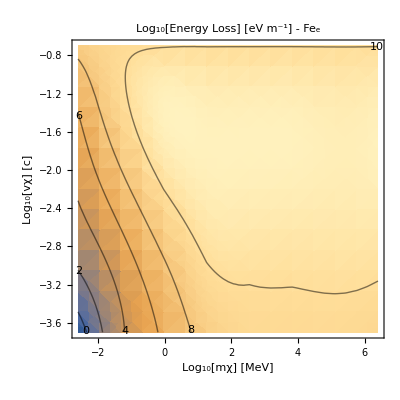

```mathematica
EnergyLoss`PlotEL[FeELOutputDictSIEnhanced,"Fe_e"]
```

```mathematica
Log10[("vF")/("c")/.FeELOutputDictSIEnhanced[["fitparams"]]]
```

{-2.25085,-2.16217,-2.04363,-1.7555,-1.05023,-0.388879}

```mathematica
Log10[("ℏ""ωp")/("JpereV")/.FeELOutputDictSIEnhanced[["fitparams"]]]
```

{1.07836,1.21138,1.38919,1.82139,2.87928,3.87131}

So transition happens around the plasmon energy - weight no it doesn’t this is eV

```mathematica
Log10[("ℏ""ωp")/("JpereV")/.FeELOutputDictSIEnhanced[["fitparams"]]]
```

#### Run SiO2

```mathematica
SiO2ELOutputDictSIEnhanced = EnergyLossTableAndInterFITTotalParamsEnhanced[{2.5 10^3,2.5 10^12} ("JpereV")/("c")^2/.SIConstRepl,{2 10^-4,2 10^-1} "c" /.SIConstRepl,<|"mχ"->8,"vχ"->4|>,SiO2Totalparams,True,"SiO2ELOutputDictSIEnhanced"]
```

1 of 32

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.0000616587}. NIntegrate obtained -8.73754×10^-19 and 2.04963×10^-18 for the integral and error estimates.

For mχ = 4.45×10^-33 , vχ = 60000
L:	-8.73754×10^-19 
Prefactor:	2.08918×10^15
 (RowBox[{)^th E moment:	-0.00182543

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.0000416375}. NIntegrate obtained -1.38841×10^-21 and 2.1498×10^-20 for the integral and error estimates.

For mχ = 4.45×10^-33 , vχ = 60000
L:	-1.38841×10^-21 
Prefactor:	2.77438×10^15
 (RowBox[{)^th E moment:	-3.85198×10^-6

dEdr total: -0.00182928

2 of 32

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.000099157}. NIntegrate obtained 1.61818×10^-12 and 1.50777×10^-14 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

For mχ = 4.45×10^-33 , vχ = 600000
L:	1.61818×10^-12 
Prefactor:	2.08918×10^13
 (RowBox[{)^th E moment:	33.8067

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

For mχ = 4.45×10^-33 , vχ = 600000
L:	1.01307×10^-13 
Prefactor:	2.77438×10^13
 (RowBox[{)^th E moment:	2.81065

dEdr total: 36.6174

3 of 32

For mχ = 4.45×10^-33 , vχ = 6000000
L:	1.71706×10^-7 
Prefactor:	2.08918×10^11
 (RowBox[{)^th E moment:	35872.5

For mχ = 4.45×10^-33 , vχ = 6000000
L:	1.18112×10^-8 
Prefactor:	2.77438×10^11
 (RowBox[{)^th E moment:	3276.87

dEdr total: 39149.3

4 of 32

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.184272 
Prefactor:	2.08918×10^9
 (RowBox[{)^th E moment:	3.84977×10^8

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.0191453 
Prefactor:	2.77438×10^9
 (RowBox[{)^th E moment:	5.31162×10^7

dEdr total: 4.38094×10^8

5 of 32

For mχ = 8.5916×10^-32 , vχ = 60000
L:	5.99674×10^-14 
Prefactor:	2.08918×10^15
 (RowBox[{)^th E moment:	125.283

For mχ = 8.5916×10^-32 , vχ = 60000
L:	3.96201×10^-15 
Prefactor:	2.77438×10^15
 (RowBox[{)^th E moment:	10.9921

dEdr total: 136.275

6 of 32

For mχ = 8.5916×10^-32 , vχ = 600000
L:	1.44154×10^-9 
Prefactor:	2.08918×10^13
 (RowBox[{)^th E moment:	30116.4

For mχ = 8.5916×10^-32 , vχ = 600000
L:	9.91639×10^-11 
Prefactor:	2.77438×10^13
 (RowBox[{)^th E moment:	2751.18

dEdr total: 32867.6

7 of 32

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.00137094 
Prefactor:	2.08918×10^11
 (RowBox[{)^th E moment:	2.86414×10^8

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.0000852884 
Prefactor:	2.77438×10^11
 (RowBox[{)^th E moment:	2.36622×10^7

dEdr total: 3.10076×10^8

8 of 32

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	0.630331 
Prefactor:	2.08918×10^9
 (RowBox[{)^th E moment:	1.31688×10^9

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	0.295002 
Prefactor:	2.77438×10^9
 (RowBox[{)^th E moment:	8.18447×10^8

dEdr total: 2.13532×10^9

9 of 32

For mχ = 1.65878×10^-30 , vχ = 60000
L:	2.71×10^-11 
Prefactor:	2.08918×10^15
 (RowBox[{)^th E moment:	56616.9

For mχ = 1.65878×10^-30 , vχ = 60000
L:	1.8633×10^-12 
Prefactor:	2.77438×10^15
 (RowBox[{)^th E moment:	5169.48

dEdr total: 61786.4

10 of 32

For mχ = 1.65878×10^-30 , vχ = 600000
L:	8.64356×10^-6 
Prefactor:	2.08918×10^13
 (RowBox[{)^th E moment:	1.8058×10^8

For mχ = 1.65878×10^-30 , vχ = 600000
L:	5.77319×10^-7 
Prefactor:	2.77438×10^13
 (RowBox[{)^th E moment:	1.6017×10^7

dEdr total: 1.96597×10^8

11 of 32

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.247989 
Prefactor:	2.08918×10^11
 (RowBox[{)^th E moment:	5.18095×10^10

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.0567392 
Prefactor:	2.77438×10^11
 (RowBox[{)^th E moment:	1.57416×10^10

dEdr total: 6.75511×10^10

12 of 32

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	0.910314 
Prefactor:	2.08918×10^9
 (RowBox[{)^th E moment:	1.90181×10^9

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	0.462107 
Prefactor:	2.77438×10^9
 (RowBox[{)^th E moment:	1.28206×10^9

dEdr total: 3.18387×10^9

13 of 32

For mχ = 3.2026×10^-29 , vχ = 60000
L:	5.13253×10^-8 
Prefactor:	2.08918×10^15
 (RowBox[{)^th E moment:	1.07228×10^8

For mχ = 3.2026×10^-29 , vχ = 60000
L:	3.55602×10^-9 
Prefactor:	2.77438×10^15
 (RowBox[{)^th E moment:	9.86574×10^6

dEdr total: 1.17094×10^8

14 of 32

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.000692923 
Prefactor:	2.08918×10^13
 (RowBox[{)^th E moment:	1.44764×10^10

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.000102671 
Prefactor:	2.77438×10^13
 (RowBox[{)^th E moment:	2.84847×10^9

dEdr total: 1.73249×10^10

15 of 32

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.31538 
Prefactor:	2.08918×10^11
 (RowBox[{)^th E moment:	6.58885×10^10

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.0963941 
Prefactor:	2.77438×10^11
 (RowBox[{)^th E moment:	2.67434×10^10

dEdr total: 9.26319×10^10

16 of 32

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	0.96694 
Prefactor:	2.08918×10^9
 (RowBox[{)^th E moment:	2.02011×10^9

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	0.495406 
Prefactor:	2.77438×10^9
 (RowBox[{)^th E moment:	1.37444×10^9

dEdr total: 3.39456×10^9

17 of 32

For mχ = 6.18325×10^-28 , vχ = 60000
L:	7.93995×10^-7 
Prefactor:	2.08918×10^15
 (RowBox[{)^th E moment:	1.6588×10^9

For mχ = 6.18325×10^-28 , vχ = 60000
L:	1.2611×10^-7 
Prefactor:	2.77438×10^15
 (RowBox[{)^th E moment:	3.49876×10^8

dEdr total: 2.00868×10^9

18 of 32

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.000883072 
Prefactor:	2.08918×10^13
 (RowBox[{)^th E moment:	1.8449×10^10

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.00015105 
Prefactor:	2.77438×10^13
 (RowBox[{)^th E moment:	4.1907×10^9

dEdr total: 2.26397×10^10

19 of 32

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.319602 
Prefactor:	2.08918×10^11
 (RowBox[{)^th E moment:	6.67708×10^10

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.0989875 
Prefactor:	2.77438×10^11
 (RowBox[{)^th E moment:	2.74629×10^10

dEdr total: 9.42336×10^10

20 of 32

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	0.970589 
Prefactor:	2.08918×10^9
 (RowBox[{)^th E moment:	2.02774×10^9

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	0.497651 
Prefactor:	2.77438×10^9
 (RowBox[{)^th E moment:	1.38067×10^9

dEdr total: 3.40841×10^9

21 of 32

For mχ = 1.1938×10^-26 , vχ = 60000
L:	8.99096×10^-7 
Prefactor:	2.08918×10^15
 (RowBox[{)^th E moment:	1.87837×10^9

For mχ = 1.1938×10^-26 , vχ = 60000
L:	1.53627×10^-7 
Prefactor:	2.77438×10^15
 (RowBox[{)^th E moment:	4.26218×10^8

dEdr total: 2.30459×10^9

22 of 32

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.000893943 
Prefactor:	2.08918×10^13
 (RowBox[{)^th E moment:	1.86761×10^10

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.0001542 
Prefactor:	2.77438×10^13
 (RowBox[{)^th E moment:	4.2781×10^9

dEdr total: 2.29542×10^10

23 of 32

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.319829 
Prefactor:	2.08918×10^11
 (RowBox[{)^th E moment:	6.68182×10^10

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.0991232 
Prefactor:	2.77438×10^11
 (RowBox[{)^th E moment:	2.75005×10^10

dEdr total: 9.43187×10^10

24 of 32

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	0.970902 
Prefactor:	2.08918×10^9
 (RowBox[{)^th E moment:	2.02839×10^9

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	0.500327 
Prefactor:	2.77438×10^9
 (RowBox[{)^th E moment:	1.3881×10^9

dEdr total: 3.41649×10^9

25 of 32

For mχ = 2.30487×10^-25 , vχ = 60000
L:	9.03512×10^-7 
Prefactor:	2.08918×10^15
 (RowBox[{)^th E moment:	1.8876×10^9

For mχ = 2.30487×10^-25 , vχ = 60000
L:	1.55161×10^-7 
Prefactor:	2.77438×10^15
 (RowBox[{)^th E moment:	4.30474×10^8

dEdr total: 2.31808×10^9

26 of 32

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.000895306 
Prefactor:	2.08918×10^13
 (RowBox[{)^th E moment:	1.87046×10^10

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.000155285 
Prefactor:	2.77438×10^13
 (RowBox[{)^th E moment:	4.30819×10^9

dEdr total: 2.30128×10^10

27 of 32

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.317869 
Prefactor:	2.08918×10^11
 (RowBox[{)^th E moment:	6.64085×10^10

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.0984098 
Prefactor:	2.77438×10^11
 (RowBox[{)^th E moment:	2.73026×10^10

dEdr total: 9.37111×10^10

28 of 32

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	0.971736 
Prefactor:	2.08918×10^9
 (RowBox[{)^th E moment:	2.03013×10^9

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	0.497427 
Prefactor:	2.77438×10^9
 (RowBox[{)^th E moment:	1.38005×10^9

dEdr total: 3.41018×10^9

29 of 32

For mχ = 4.45×10^-24 , vχ = 60000
L:	9.18449×10^-7 
Prefactor:	2.08918×10^15
 (RowBox[{)^th E moment:	1.91881×10^9

For mχ = 4.45×10^-24 , vχ = 60000
L:	1.54846×10^-7 
Prefactor:	2.77438×10^15
 (RowBox[{)^th E moment:	4.296×10^8

dEdr total: 2.34841×10^9

30 of 32

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.000908874 
Prefactor:	2.08918×10^13
 (RowBox[{)^th E moment:	1.8988×10^10

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.000158363 
Prefactor:	2.77438×10^13
 (RowBox[{)^th E moment:	4.39358×10^9

dEdr total: 2.33816×10^10

31 of 32

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.319688 
Prefactor:	2.08918×10^11
 (RowBox[{)^th E moment:	6.67887×10^10

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.0999665 
Prefactor:	2.77438×10^11
 (RowBox[{)^th E moment:	2.77345×10^10

dEdr total: 9.45232×10^10

32 of 32

For mχ = 4.45×10^-24 , vχ = 60000000
L:	0.975228 
Prefactor:	2.08918×10^9
 (RowBox[{)^th E moment:	2.03743×10^9

For mχ = 4.45×10^-24 , vχ = 60000000
L:	0.500365 
Prefactor:	2.77438×10^9
 (RowBox[{)^th E moment:	1.3882×10^9

dEdr total: 3.42563×10^9

<|f→InterpolatingFunction[…],mχMesh→{{4.45×10^-33,4.45×10^-33,4.45×10^-33,4.45×10^-33},{8.5916×10^-32,8.5916×10^-32,8.5916×10^-32,8.5916×10^-32},{1.65878×10^-30,1.65878×10^-30,1.65878×10^-30,1.65878×10^-30},{3.2026×10^-29,3.2026×10^-29,3.2026×10^-29,3.2026×10^-29},{6.18325×10^-28,6.18325×10^-28,6.18325×10^-28,6.18325×10^-28},{1.1938×10^-26,1.1938×10^-26,1.1938×10^-26,1.1938×10^-26},{2.30487×10^-25,2.30487×10^-25,2.30487×10^-25,2.30487×10^-25},{4.45×10^-24,4.45×10^-24,4.45×10^-24,4.45×10^-24}},vχMesh→{{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000}},EnergyLossMesh→{{-0.00182928,36.6174,39149.3,4.38094×10^8},{136.275,32867.6,3.10076×10^8,2.13532×10^9},{61786.4,1.96597×10^8,6.75511×10^10,3.18387×10^9},{1.17094×10^8,1.73249×10^10,9.26319×10^10,3.39456×10^9},{2.00868×10^9,2.26397×10^10,9.42336×10^10,3.40841×10^9},{2.30459×10^9,2.29542×10^10,9.43187×10^10,3.41649×10^9},{2.31808×10^9,2.30128×10^10,9.37111×10^10,3.41018×10^9},{2.34841×10^9,2.33816×10^10,9.45232×10^10,3.42563×10^9}},fitparams→{{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.07027×10^29,qF→2.2927×10^10,vF→2.65511×10^6,μ→3.21109×10^-18,ωp→3.60151×10^16,α→1/137,χ→0.512371,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→801.791,nI→5.08784×10^28,Z→8,M→9.27329×10^-26,EF→3.21109×10^-18,ωi→3.60151×10^16,νi→2.11534×10^16,Ai→0.552697,ωedgei→0},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→2.0121×10^30,qF→3.90562×10^10,vF→4.52297×10^6,μ→9.3183×10^-18,ωp→8.0075×10^16,α→1/137,χ→0.392567,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→2326.72,nI→2.51512×10^29,Z→8,M→9.27329×10^-26,EF→9.3183×10^-18,ωi→8.0075×10^16,νi→6.06034×10^16,Ai→0.0871584,ωedgei→0}},fname→SiO2ELOutputDictSIEnhanced,kinlist→<|mχ→{4.45×10^-33,8.5916×10^-32,1.65878×10^-30,3.2026×10^-29,6.18325×10^-28,1.1938×10^-26,2.30487×10^-25,4.45×10^-24},vχ→{60000,600000,6000000,60000000}|>,meshdims→<|mχ→8,vχ→4|>,timesMesh→{{1145.4,306.202,174.39,7.21157},{330.427,190.735,1.46477,36.7155},{92.8267,6.4011,10.9156,65.0267},{11.2188,6.78391,34.837,99.0979},{10.8153,43.4457,141.187,231.37},{70.6122,153.358,234.649,262.445},{169.385,218.32,871.344,324.213},{264.042,517.44,312.648,316.086}},totalTime→6661.01|>

#### Plot SiO2

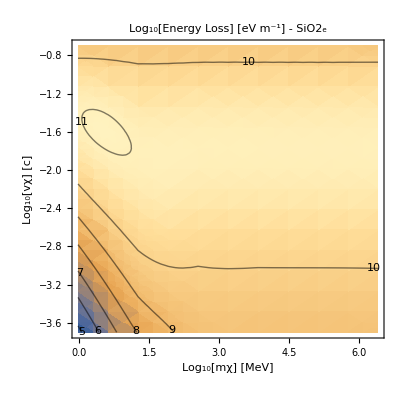

```mathematica
EnergyLoss`PlotEL[SiO2ELOutputDictSIEnhanced,"SiO2_e"]
```

```mathematica
Log10[("vF")/("c")/.SiO2ELOutputDictSIEnhanced[["fitparams"]]]
```

{-2.05304,-1.8217}

#### Run MgO

```mathematica
MgOELOutputDictSIEnhanced = EnergyLossTableAndInterFITTotalParamsEnhanced[{2.5 10^3,2.5 10^12} ("JpereV")/("c")^2/.SIConstRepl,{2 10^-4,2 10^-1} "c" /.SIConstRepl,<|"mχ"->8,"vχ"->4|>,MgOTotalparams,True,"MgOELOutputDictSIEnhanced"]
```

1 of 32

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.0000486715}. NIntegrate obtained 2.11303×10^-16 and 2.56787×10^-17 for the integral and error estimates.

For mχ = 4.45×10^-33 , vχ = 60000
L:	2.11303×10^-16 
Prefactor:	3.99192×10^13
 (RowBox[{)^th E moment:	0.00843506

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.0000429724}. NIntegrate obtained 3.2963×10^-17 and 4.83587×10^-18 for the integral and error estimates.

For mχ = 4.45×10^-33 , vχ = 60000
L:	3.2963×10^-17 
Prefactor:	5.73915×10^14
 (RowBox[{)^th E moment:	0.018918

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.0000355717}. NIntegrate obtained 2.00662×10^-17 and 2.16288×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

For mχ = 4.45×10^-33 , vχ = 60000
L:	2.00662×10^-17 
Prefactor:	4.00973×10^14
 (RowBox[{)^th E moment:	0.00804602

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

For mχ = 4.45×10^-33 , vχ = 60000
L:	2.70409×10^-21 
Prefactor:	1.00279×10^16
 (RowBox[{)^th E moment:	0.0000271164

dEdr total: 0.0354262

2 of 32

For mχ = 4.45×10^-33 , vχ = 600000
L:	3.45117×10^-12 
Prefactor:	3.99192×10^11
 (RowBox[{)^th E moment:	1.37768

For mχ = 4.45×10^-33 , vχ = 600000
L:	5.43559×10^-13 
Prefactor:	5.73915×10^12
 (RowBox[{)^th E moment:	3.11957

For mχ = 4.45×10^-33 , vχ = 600000
L:	3.51632×10^-13 
Prefactor:	4.00973×10^12
 (RowBox[{)^th E moment:	1.40995

For mχ = 4.45×10^-33 , vχ = 600000
L:	2.46016×10^-13 
Prefactor:	1.00279×10^14
 (RowBox[{)^th E moment:	24.6702

dEdr total: 30.5774

3 of 32

For mχ = 4.45×10^-33 , vχ = 6000000
L:	3.53381×10^-7 
Prefactor:	3.99192×10^9
 (RowBox[{)^th E moment:	1410.67

For mχ = 4.45×10^-33 , vχ = 6000000
L:	5.56519×10^-8 
Prefactor:	5.73915×10^10
 (RowBox[{)^th E moment:	3193.95

For mχ = 4.45×10^-33 , vχ = 6000000
L:	3.60351×10^-8 
Prefactor:	4.00973×10^10
 (RowBox[{)^th E moment:	1444.91

For mχ = 4.45×10^-33 , vχ = 6000000
L:	3.63853×10^-8 
Prefactor:	1.00279×10^12
 (RowBox[{)^th E moment:	36486.9

dEdr total: 42536.4

4 of 32

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.437304 
Prefactor:	3.99192×10^7
 (RowBox[{)^th E moment:	1.74568×10^7

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.253927 
Prefactor:	5.73915×10^8
 (RowBox[{)^th E moment:	1.45733×10^8

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.220169 
Prefactor:	4.00973×10^8
 (RowBox[{)^th E moment:	8.82817×10^7

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.024679 
Prefactor:	1.00279×10^10
 (RowBox[{)^th E moment:	2.47478×10^8

dEdr total: 4.9895×10^8

5 of 32

For mχ = 8.5916×10^-32 , vχ = 60000
L:	1.23861×10^-13 
Prefactor:	3.99192×10^13
 (RowBox[{)^th E moment:	4.94444

For mχ = 8.5916×10^-32 , vχ = 60000
L:	1.94887×10^-14 
Prefactor:	5.73915×10^14
 (RowBox[{)^th E moment:	11.1849

For mχ = 8.5916×10^-32 , vχ = 60000
L:	1.26164×10^-14 
Prefactor:	4.00973×10^14
 (RowBox[{)^th E moment:	5.05885

For mχ = 8.5916×10^-32 , vχ = 60000
L:	1.14537×10^-14 
Prefactor:	1.00279×10^16
 (RowBox[{)^th E moment:	114.856

dEdr total: 136.045

6 of 32

For mχ = 8.5916×10^-32 , vχ = 600000
L:	2.98474×10^-9 
Prefactor:	3.99192×10^11
 (RowBox[{)^th E moment:	1191.49

For mχ = 8.5916×10^-32 , vχ = 600000
L:	4.71293×10^-10 
Prefactor:	5.73915×10^12
 (RowBox[{)^th E moment:	2704.83

For mχ = 8.5916×10^-32 , vχ = 600000
L:	3.05404×10^-10 
Prefactor:	4.00973×10^12
 (RowBox[{)^th E moment:	1224.59

For mχ = 8.5916×10^-32 , vχ = 600000
L:	3.05471×10^-10 
Prefactor:	1.00279×10^14
 (RowBox[{)^th E moment:	30632.4

dEdr total: 35753.3

7 of 32

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.00429969 
Prefactor:	3.99192×10^9
 (RowBox[{)^th E moment:	1.7164×10^7

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.000609617 
Prefactor:	5.73915×10^10
 (RowBox[{)^th E moment:	3.49869×10^7

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.000397961 
Prefactor:	4.00973×10^10
 (RowBox[{)^th E moment:	1.59572×10^7

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.00024948 
Prefactor:	1.00279×10^12
 (RowBox[{)^th E moment:	2.50177×10^8

dEdr total: 3.18285×10^8

8 of 32

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	1.02424 
Prefactor:	3.99192×10^7
 (RowBox[{)^th E moment:	4.08869×10^7

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	0.70857 
Prefactor:	5.73915×10^8
 (RowBox[{)^th E moment:	4.06659×10^8

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	0.65025 
Prefactor:	4.00973×10^8
 (RowBox[{)^th E moment:	2.60733×10^8

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	0.293459 
Prefactor:	1.00279×10^10
 (RowBox[{)^th E moment:	2.94279×10^9

dEdr total: 3.65107×10^9

9 of 32

For mχ = 1.65878×10^-30 , vχ = 60000
L:	5.73834×10^-11 
Prefactor:	3.99192×10^13
 (RowBox[{)^th E moment:	2290.7

For mχ = 1.65878×10^-30 , vχ = 60000
L:	9.11908×10^-12 
Prefactor:	5.73915×10^14
 (RowBox[{)^th E moment:	5233.58

For mχ = 1.65878×10^-30 , vχ = 60000
L:	5.92185×10^-12 
Prefactor:	4.00973×10^14
 (RowBox[{)^th E moment:	2374.5

For mχ = 1.65878×10^-30 , vχ = 60000
L:	5.7371×10^-12 
Prefactor:	1.00279×10^16
 (RowBox[{)^th E moment:	57531.1

dEdr total: 67429.9

10 of 32

For mχ = 1.65878×10^-30 , vχ = 600000
L:	0.0000320185 
Prefactor:	3.99192×10^11
 (RowBox[{)^th E moment:	1.27815×10^7

For mχ = 1.65878×10^-30 , vχ = 600000
L:	5.84627×10^-6 
Prefactor:	5.73915×10^12
 (RowBox[{)^th E moment:	3.35526×10^7

For mχ = 1.65878×10^-30 , vχ = 600000
L:	3.94049×10^-6 
Prefactor:	4.00973×10^12
 (RowBox[{)^th E moment:	1.58003×10^7

For mχ = 1.65878×10^-30 , vχ = 600000
L:	1.64857×10^-6 
Prefactor:	1.00279×10^14
 (RowBox[{)^th E moment:	1.65317×10^8

dEdr total: 2.27452×10^8

11 of 32

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.509263 
Prefactor:	3.99192×10^9
 (RowBox[{)^th E moment:	2.03294×10^9

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.311318 
Prefactor:	5.73915×10^10
 (RowBox[{)^th E moment:	1.7867×10^10

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.274775 
Prefactor:	4.00973×10^10
 (RowBox[{)^th E moment:	1.10177×10^10

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.0610451 
Prefactor:	1.00279×10^12
 (RowBox[{)^th E moment:	6.12155×10^10

dEdr total: 9.21332×10^10

12 of 32

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	1.41205 
Prefactor:	3.99192×10^7
 (RowBox[{)^th E moment:	5.6368×10^7

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	0.999237 
Prefactor:	5.73915×10^8
 (RowBox[{)^th E moment:	5.73478×10^8

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	0.922325 
Prefactor:	4.00973×10^8
 (RowBox[{)^th E moment:	3.69828×10^8

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	0.474931 
Prefactor:	1.00279×10^10
 (RowBox[{)^th E moment:	4.76256×10^9

dEdr total: 5.76224×10^9

13 of 32

For mχ = 3.2026×10^-29 , vχ = 60000
L:	2.14064×10^-7 
Prefactor:	3.99192×10^13
 (RowBox[{)^th E moment:	8.54528×10^6

For mχ = 3.2026×10^-29 , vχ = 60000
L:	4.31587×10^-8 
Prefactor:	5.73915×10^14
 (RowBox[{)^th E moment:	2.47695×10^7

For mχ = 3.2026×10^-29 , vχ = 60000
L:	2.97574×10^-8 
Prefactor:	4.00973×10^14
 (RowBox[{)^th E moment:	1.19319×10^7

For mχ = 3.2026×10^-29 , vχ = 60000
L:	9.12407×10^-9 
Prefactor:	1.00279×10^16
 (RowBox[{)^th E moment:	9.14954×10^7

dEdr total: 1.36742×10^8

14 of 32

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.00188777 
Prefactor:	3.99192×10^11
 (RowBox[{)^th E moment:	7.53584×10^8

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.000672892 
Prefactor:	5.73915×10^12
 (RowBox[{)^th E moment:	3.86183×10^9

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.000528375 
Prefactor:	4.00973×10^12
 (RowBox[{)^th E moment:	2.11864×10^9

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.000177627 
Prefactor:	1.00279×10^14
 (RowBox[{)^th E moment:	1.78123×10^10

dEdr total: 2.45464×10^10

15 of 32

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.595321 
Prefactor:	3.99192×10^9
 (RowBox[{)^th E moment:	2.37648×10^9

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.379855 
Prefactor:	5.73915×10^10
 (RowBox[{)^th E moment:	2.18005×10^10

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.340276 
Prefactor:	4.00973×10^10
 (RowBox[{)^th E moment:	1.36442×10^10

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.0968777 
Prefactor:	1.00279×10^12
 (RowBox[{)^th E moment:	9.71481×10^10

dEdr total: 1.34969×10^11

16 of 32

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	1.49014 
Prefactor:	3.99192×10^7
 (RowBox[{)^th E moment:	5.94854×10^7

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	1.05515 
Prefactor:	5.73915×10^8
 (RowBox[{)^th E moment:	6.05568×10^8

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	0.977997 
Prefactor:	4.00973×10^8
 (RowBox[{)^th E moment:	3.9215×10^8

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	0.510842 
Prefactor:	1.00279×10^10
 (RowBox[{)^th E moment:	5.12268×10^9

dEdr total: 6.17988×10^9

17 of 32

For mχ = 6.18325×10^-28 , vχ = 60000
L:	2.07402×10^-6 
Prefactor:	3.99192×10^13
 (RowBox[{)^th E moment:	8.27935×10^7

For mχ = 6.18325×10^-28 , vχ = 60000
L:	7.62975×10^-7 
Prefactor:	5.73915×10^14
 (RowBox[{)^th E moment:	4.37883×10^8

For mχ = 6.18325×10^-28 , vχ = 60000
L:	6.03931×10^-7 
Prefactor:	4.00973×10^14
 (RowBox[{)^th E moment:	2.4216×10^8

For mχ = 6.18325×10^-28 , vχ = 60000
L:	2.15117×10^-7 
Prefactor:	1.00279×10^16
 (RowBox[{)^th E moment:	2.15717×10^9

dEdr total: 2.92001×10^9

18 of 32

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.00227905 
Prefactor:	3.99192×10^11
 (RowBox[{)^th E moment:	9.09781×10^8

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.0008578 
Prefactor:	5.73915×10^12
 (RowBox[{)^th E moment:	4.92304×10^9

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.000683651 
Prefactor:	4.00973×10^12
 (RowBox[{)^th E moment:	2.74126×10^9

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.000249912 
Prefactor:	1.00279×10^14
 (RowBox[{)^th E moment:	2.50609×10^10

dEdr total: 3.3635×10^10

19 of 32

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.60078 
Prefactor:	3.99192×10^9
 (RowBox[{)^th E moment:	2.39827×10^9

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.384118 
Prefactor:	5.73915×10^10
 (RowBox[{)^th E moment:	2.20451×10^10

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.344232 
Prefactor:	4.00973×10^10
 (RowBox[{)^th E moment:	1.38028×10^10

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.0993105 
Prefactor:	1.00279×10^12
 (RowBox[{)^th E moment:	9.95878×10^10

dEdr total: 1.37834×10^11

20 of 32

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	1.49493 
Prefactor:	3.99192×10^7
 (RowBox[{)^th E moment:	5.96764×10^7

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	1.06341 
Prefactor:	5.73915×10^8
 (RowBox[{)^th E moment:	6.10309×10^8

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	0.981729 
Prefactor:	4.00973×10^8
 (RowBox[{)^th E moment:	3.93647×10^8

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	0.513268 
Prefactor:	1.00279×10^10
 (RowBox[{)^th E moment:	5.14701×10^9

dEdr total: 6.21064×10^9

21 of 32

For mχ = 1.1938×10^-26 , vχ = 60000
L:	2.28159×10^-6 
Prefactor:	3.99192×10^13
 (RowBox[{)^th E moment:	9.10794×10^7

For mχ = 1.1938×10^-26 , vχ = 60000
L:	8.6344×10^-7 
Prefactor:	5.73915×10^14
 (RowBox[{)^th E moment:	4.95542×10^8

For mχ = 1.1938×10^-26 , vχ = 60000
L:	6.88019×10^-7 
Prefactor:	4.00973×10^14
 (RowBox[{)^th E moment:	2.75877×10^8

For mχ = 1.1938×10^-26 , vχ = 60000
L:	2.56592×10^-7 
Prefactor:	1.00279×10^16
 (RowBox[{)^th E moment:	2.57308×10^9

dEdr total: 3.43558×10^9

22 of 32

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.00230151 
Prefactor:	3.99192×10^11
 (RowBox[{)^th E moment:	9.18746×10^8

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.000868182 
Prefactor:	5.73915×10^12
 (RowBox[{)^th E moment:	4.98263×10^9

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.000692695 
Prefactor:	4.00973×10^12
 (RowBox[{)^th E moment:	2.77752×10^9

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.000254115 
Prefactor:	1.00279×10^14
 (RowBox[{)^th E moment:	2.54824×10^10

dEdr total: 3.41613×10^10

23 of 32

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.600121 
Prefactor:	3.99192×10^9
 (RowBox[{)^th E moment:	2.39564×10^9

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.384748 
Prefactor:	5.73915×10^10
 (RowBox[{)^th E moment:	2.20813×10^10

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.345117 
Prefactor:	4.00973×10^10
 (RowBox[{)^th E moment:	1.38383×10^10

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.0994385 
Prefactor:	1.00279×10^12
 (RowBox[{)^th E moment:	9.97161×10^10

dEdr total: 1.38031×10^11

24 of 32

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	1.49462 
Prefactor:	3.99192×10^7
 (RowBox[{)^th E moment:	5.96641×10^7

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	1.0606 
Prefactor:	5.73915×10^8
 (RowBox[{)^th E moment:	6.08696×10^8

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	0.982983 
Prefactor:	4.00973×10^8
 (RowBox[{)^th E moment:	3.9415×10^8

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	0.512927 
Prefactor:	1.00279×10^10
 (RowBox[{)^th E moment:	5.14359×10^9

dEdr total: 6.2061×10^9

25 of 32

For mχ = 2.30487×10^-25 , vχ = 60000
L:	2.28206×10^-6 
Prefactor:	3.99192×10^13
 (RowBox[{)^th E moment:	9.10981×10^7

For mχ = 2.30487×10^-25 , vχ = 60000
L:	8.82405×10^-7 
Prefactor:	5.73915×10^14
 (RowBox[{)^th E moment:	5.06426×10^8

For mχ = 2.30487×10^-25 , vχ = 60000
L:	6.79875×10^-7 
Prefactor:	4.00973×10^14
 (RowBox[{)^th E moment:	2.72611×10^8

For mχ = 2.30487×10^-25 , vχ = 60000
L:	2.58917×10^-7 
Prefactor:	1.00279×10^16
 (RowBox[{)^th E moment:	2.5964×10^9

dEdr total: 3.46653×10^9

26 of 32

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.00229458 
Prefactor:	3.99192×10^11
 (RowBox[{)^th E moment:	9.15981×10^8

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.000867966 
Prefactor:	5.73915×10^12
 (RowBox[{)^th E moment:	4.98139×10^9

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.000692574 
Prefactor:	4.00973×10^12
 (RowBox[{)^th E moment:	2.77704×10^9

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.000252938 
Prefactor:	1.00279×10^14
 (RowBox[{)^th E moment:	2.53644×10^10

dEdr total: 3.40388×10^10

27 of 32

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	-1.60819×10^-13 
Prefactor:	3.99192×10^9
 (RowBox[{)^th E moment:	-0.000641979

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.3737 
Prefactor:	5.73915×10^10
 (RowBox[{)^th E moment:	2.14472×10^10

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.326682 
Prefactor:	4.00973×10^10
 (RowBox[{)^th E moment:	1.30991×10^10

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.0994209 
Prefactor:	1.00279×10^12
 (RowBox[{)^th E moment:	9.96984×10^10

dEdr total: 1.34245×10^11

28 of 32

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	1.49636 
Prefactor:	3.99192×10^7
 (RowBox[{)^th E moment:	5.97337×10^7

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	1.06183 
Prefactor:	5.73915×10^8
 (RowBox[{)^th E moment:	6.09398×10^8

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	0.981203 
Prefactor:	4.00973×10^8
 (RowBox[{)^th E moment:	3.93436×10^8

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	0.513516 
Prefactor:	1.00279×10^10
 (RowBox[{)^th E moment:	5.14949×10^9

dEdr total: 6.21206×10^9

29 of 32

For mχ = 4.45×10^-24 , vχ = 60000
L:	2.27318×10^-6 
Prefactor:	3.99192×10^13
 (RowBox[{)^th E moment:	9.07438×10^7

For mχ = 4.45×10^-24 , vχ = 60000
L:	8.67351×10^-7 
Prefactor:	5.73915×10^14
 (RowBox[{)^th E moment:	4.97786×10^8

For mχ = 4.45×10^-24 , vχ = 60000
L:	7.44625×10^-7 
Prefactor:	4.00973×10^14
 (RowBox[{)^th E moment:	2.98574×10^8

For mχ = 4.45×10^-24 , vχ = 60000
L:	2.59433×10^-7 
Prefactor:	1.00279×10^16
 (RowBox[{)^th E moment:	2.60158×10^9

dEdr total: 3.48868×10^9

30 of 32

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.00231359 
Prefactor:	3.99192×10^11
 (RowBox[{)^th E moment:	9.23567×10^8

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.000883355 
Prefactor:	5.73915×10^12
 (RowBox[{)^th E moment:	5.06971×10^9

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.000692421 
Prefactor:	4.00973×10^12
 (RowBox[{)^th E moment:	2.77642×10^9

For mχ = 4.45×10^-24 , vχ = 600000
L:	-3.87825×10^-17 
Prefactor:	1.00279×10^14
 (RowBox[{)^th E moment:	-0.00388908

dEdr total: 8.7697×10^9

31 of 32

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.567041 
Prefactor:	3.99192×10^9
 (RowBox[{)^th E moment:	2.26358×10^9

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.382398 
Prefactor:	5.73915×10^10
 (RowBox[{)^th E moment:	2.19464×10^10

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.342041 
Prefactor:	4.00973×10^10
 (RowBox[{)^th E moment:	1.37149×10^10

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.0994416 
Prefactor:	1.00279×10^12
 (RowBox[{)^th E moment:	9.97192×10^10

dEdr total: 1.37644×10^11

32 of 32

For mχ = 4.45×10^-24 , vχ = 60000000
L:	1.49809 
Prefactor:	3.99192×10^7
 (RowBox[{)^th E moment:	5.98026×10^7

For mχ = 4.45×10^-24 , vχ = 60000000
L:	1.06954 
Prefactor:	5.73915×10^8
 (RowBox[{)^th E moment:	6.13823×10^8

For mχ = 4.45×10^-24 , vχ = 60000000
L:	0.988104 
Prefactor:	4.00973×10^8
 (RowBox[{)^th E moment:	3.96203×10^8

For mχ = 4.45×10^-24 , vχ = 60000000
L:	0.516322 
Prefactor:	1.00279×10^10
 (RowBox[{)^th E moment:	5.17763×10^9

dEdr total: 6.24746×10^9

<|f→InterpolatingFunction[…],mχMesh→{{4.45×10^-33,4.45×10^-33,4.45×10^-33,4.45×10^-33},{8.5916×10^-32,8.5916×10^-32,8.5916×10^-32,8.5916×10^-32},{1.65878×10^-30,1.65878×10^-30,1.65878×10^-30,1.65878×10^-30},{3.2026×10^-29,3.2026×10^-29,3.2026×10^-29,3.2026×10^-29},{6.18325×10^-28,6.18325×10^-28,6.18325×10^-28,6.18325×10^-28},{1.1938×10^-26,1.1938×10^-26,1.1938×10^-26,1.1938×10^-26},{2.30487×10^-25,2.30487×10^-25,2.30487×10^-25,2.30487×10^-25},{4.45×10^-24,4.45×10^-24,4.45×10^-24,4.45×10^-24}},vχMesh→{{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000}},EnergyLossMesh→{{0.0354262,30.5774,42536.4,4.9895×10^8},{136.045,35753.3,3.18285×10^8,3.65107×10^9},{67429.9,2.27452×10^8,9.21332×10^10,5.76224×10^9},{1.36742×10^8,2.45464×10^10,1.34969×10^11,6.17988×10^9},{2.92001×10^9,3.3635×10^10,1.37834×10^11,6.21064×10^9},{3.43558×10^9,3.41613×10^10,1.38031×10^11,6.2061×10^9},{3.46653×10^9,3.40388×10^10,1.34245×10^11,6.21206×10^9},{3.48868×10^9,8.7697×10^9,1.37644×10^11,6.24746×10^9}},fitparams→{{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→1.50385×10^29,qF→1.64516×10^10,vF→1.90521×10^6,μ→1.65338×10^-18,ωp→2.18914×10^16,α→1/137,χ→0.604859,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→412.839,nI→1.87981×10^28,Z→8,M→9.27329×10^-26,EF→1.65338×10^-18,ωi→2.18914×10^16,νi→4.25006×10^15,Ai→0.039834,ωedgei→0},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→3.58115×10^29,qF→2.19692×10^10,vF→2.54418×10^6,μ→2.94839×10^-18,ωp→3.37819×10^16,α→1/137,χ→0.523421,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→736.197,nI→4.47644×10^28,Z→8,M→9.27329×10^-26,EF→2.94839×10^-18,ωi→3.37819×10^16,νi→5.06751×10^15,Ai→0.180092,ωedgei→0},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.37351×10^29,qF→2.34828×10^10,vF→2.71947×10^6,μ→3.36866×10^-18,ωp→3.73325×10^16,α→1/137,χ→0.506271,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→841.135,nI→5.46689×10^28,Z→8,M→9.27329×10^-26,EF→3.36866×10^-18,ωi→3.73325×10^16,νi→5.23006×10^15,Ai→0.0963866,ωedgei→0},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→1.61838×10^30,qF→3.63218×10^10,vF→4.20631×10^6,μ→8.05919×10^-18,ωp→7.18146×10^16,α→1/137,χ→0.407075,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→2012.33,nI→2.02298×10^29,Z→8,M→9.27329×10^-26,EF→8.05919×10^-18,ωi→7.18146×10^16,νi→1.12397×10^17,Ai→0.421157,ωedgei→0}},fname→MgOELOutputDictSIEnhanced,kinlist→<|mχ→{4.45×10^-33,8.5916×10^-32,1.65878×10^-30,3.2026×10^-29,6.18325×10^-28,1.1938×10^-26,2.30487×10^-25,4.45×10^-24},vχ→{60000,600000,6000000,60000000}|>,meshdims→<|mχ→8,vχ→4|>,timesMesh→{{1445.12,680.341,193.613,27.4871},{547.58,251.843,3.19096,91.3971},{130.362,9.54612,48.0763,106.882},{22.732,9.15579,84.6618,206.176},{35.6022,111.074,290.974,436.876},{161.554,309.716,531.229,474.78},{395.829,454.864,879.849,477.154},{437.59,649.084,610.268,644.851}},totalTime→10759.5|>

#### Plot MgO

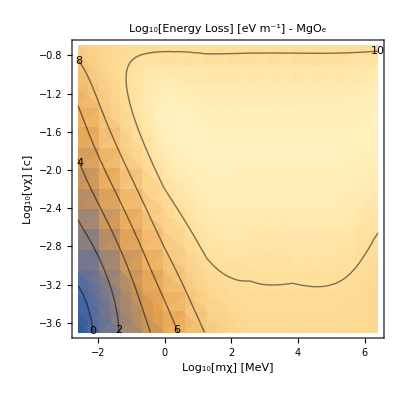

```mathematica
EnergyLoss`PlotEL[MgOELOutputDictSIEnhanced,"MgO_e"]
```

```mathematica
Log10[("vF")/("c")/.MgOELOutputDictSIEnhanced[["fitparams"]]]
```

{-2.19718,-2.07157,-2.04264,-1.85322}